# Gametic Selection, Sex-Ratio Bias, and Transitions Between Sex-Determining Systems

## Michael F Scott, Matthew M Osmond, Sarah P Otto

# A. Offspring control

## Life-cycle

Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}];
Subscript[fHapSel, x_,y_,z_,sex_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex]/Subscript[wbarHap, sex]
```

Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if ESD wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female ESD wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the ESD*)
Subscript[psex, zM_,xP_,m,female]->k
};
```

Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Segregation rules with female and male-specific meiotic drive (individuals of sex i who are heterozygous at the viablilty locus produce α_i% A haplotypes and 1-α_i% a haplotypes before selection)

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,A,z1_]->Subscript[α, male] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,a,z1_]->(1-Subscript[α, male]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,A,z1_]->Subscript[α, male] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,a,z1_]->(1-Subscript[α, male]),
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,female,x1_,A,z1_]->Subscript[α, female] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,female,x1_,A,z1_]->Subscript[α, female] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,A,z1_]->Subscript[α, male](1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,a,z1_]->(1-Subscript[α, male])(1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,A,z1_]->Subscript[α, male] r,
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,a,z1_]->(1-Subscript[α, male])r,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])(1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z2_]->Subscript[α, male] R,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,A,z1_]->Subscript[α, male] r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,a,z1_]->(1-Subscript[α, male])r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,A,z1_]->Subscript[α, male] (1-r),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,a,z1_]->(1-Subscript[α, male])(1-r),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] (1-R),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) (1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x1_,A,z1_]->Subscript[α, female](1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x2_,a,z1_]->(1-Subscript[α, female])(1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x2_,A,z1_]->Subscript[α, female] r,
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x1_,a,z1_]->(1-Subscript[α, female])r,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])(1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,A,z2_]->Subscript[α, female] R,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x1_,A,z1_]->Subscript[α, female] r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x2_,a,z1_]->(1-Subscript[α, female])r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x2_,A,z1_]->Subscript[α, female] (1-r),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x1_,a,z1_]->(1-Subscript[α, female])(1-r),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,A,z1_]->Subscript[α, female] R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] (1-R),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) (1-R),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(r(1-R)+(1-r)R)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])(1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z1_]->Subscript[α, male] r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z2_]->Subscript[α, male] r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z2_]->Subscript[α, male](1-r)R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z1_]->Subscript[α, male] (1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z2_]->Subscript[α, male] (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] r(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])r (1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])(1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z1_]->Subscript[α, female] r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z2_]->Subscript[α, female] r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z2_]->Subscript[α, female](1-r)R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z1_]->Subscript[α, female] r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z1_]->Subscript[α, female] (1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z2_]->Subscript[α, female] (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] r(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])r (1-R)
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

```mathematica
(*ParallelSum[Subscript[fHapNext, x,y,z,sex]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}}]//Factor*)
```

## Resident equilibrium (weak selection)

We begin with no mutations at the modifer locus

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->pXm *(1-freqYm),
Subscript[fHap, X,a,M,male]->(1-pXm)(1-freqYm),
Subscript[fHap, Y,A,M,male]->pYm freqYm,
Subscript[fHap, Y,a,M,male]->(1-pYm)freqYm,
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
};
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
(Subscript[fHapNext, Y,A,M,male]+Subscript[fHapNext, Y,a,M,male])-(Subscript[fHap, Y,A,M,male]+Subscript[fHap, Y,a,M,male])
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume weak selection in both haploids and diploids and weak meiotic drive. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
Subscript[wHap, A,sex_]->1+Subscript[sHap, sex] ϵ,
Subscript[wHap, a,sex_]->1,
Subscript[wDip, A,A,sex_]->1+ Subscript[sDip, sex] ϵ,
Subscript[wDip, A,a,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,A,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,a,sex_]->1,
Subscript[α, sex_]->1/2+Subscript[α1, sex] ϵ
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ+pXf2*ϵ^2,
pXm->pXm0+pXm1 ϵ+pXm2*ϵ^2,
pYm->pYm0+pYm1 ϵ+pYm2*ϵ^2,
freqYm->freqYm0+freqYm1 ϵ+freqYm2*ϵ^2
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-2 pXm0+2 freqYm0 pXm0-pXf0 r+pYm0 r),1/2 (pYm0-2 freqYm0 pYm0+pXf0 r-pYm0 r),1/2 (1-2 freqYm0)}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0,freqYm0}]//Flatten
```

{pYm0→pXf0,pXm0→pXf0,freqYm0→1/2}

So, with no selection or drive, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA) and half of male gametes/pollen carry the Y.

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1+2 pA^2 sDip_female-2 pA^3 sDip_female+2 pA h_female sDip_female-6 pA^2 h_female sDip_female+4 pA^3 h_female sDip_female+pA sHap_female-pA^2 sHap_female+pA sHap_male-pA^2 sHap_male+4 pA α1_female-4 pA^2 α1_female),1/2 ϵ (2 freqYm1 pA+pXf1-pXm1-pXf1 r+pYm1 r+pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male+pA sHap_female-pA^2 sHap_female-pA r sHap_female+pA^2 r sHap_female+pA r sHap_male-pA^2 r sHap_male+2 pA α1_male-2 pA^2 α1_male),1/2 ϵ (-2 freqYm1 pA+pXf1 r-pYm1 r+pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male+pA r sHap_female-pA^2 r sHap_female+pA sHap_male-pA^2 sHap_male-pA r sHap_male+pA^2 r sHap_male+2 pA α1_male-2 pA^2 α1_male),-freqYm1 ϵ}

And from these three equations we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA,freqYm1}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0,freqYm1→0},{dpAXmXf→0,dpAYmXf→0,pA→1,freqYm1→0},{dpAXmXf→((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male-2 α1_female-2 α1_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+2 α1_female+2 α1_male) (2 h_female sDip_female sDip_male-2 h_male sDip_female sDip_male-sDip_female sHap_female+2 h_female sDip_female sHap_female+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male sHap_male-2 h_male sDip_male sHap_male+4 sDip_male α1_female-8 h_male sDip_male α1_female-4 sDip_female α1_male+8 h_female sDip_female α1_male))/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3,dpAYmXf→((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male-2 α1_female-2 α1_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+2 α1_female+2 α1_male) (h_female sDip_female sDip_male-h_male sDip_female sDip_male-r sDip_female sHap_female+2 r h_female sDip_female sHap_female+sDip_male sHap_female-r sDip_male sHap_female-2 h_male sDip_male sHap_female+2 r h_male sDip_male sHap_female-sDip_female sHap_male+r sDip_female sHap_male+2 h_female sDip_female sHap_male-2 r h_female sDip_female sHap_male+r sDip_male sHap_male-2 r h_male sDip_male sHap_male+2 sDip_male α1_female-4 h_male sDip_male α1_female-2 sDip_female α1_male+4 h_female sDip_female α1_male))/(r (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3),pA→(h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+2 α1_female+2 α1_male)/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male),freqYm1→0}}

van Doorn and Kirkpatrick 2007 (SOM, page 6) give

```mathematica
vDK07=(Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male])/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male]);
```

And when there is no haploid selection or drive our result reduces to theirs

```mathematica
(pA/.realsol[[3]]/.Subscript[sHap, i_]->0/.Subscript[α1, sex_]->0)/vDK07//FullSimplify
```

1

Going to the next order in selection

```mathematica
differenceEqs2freqY=Collect[Normal[Series[differenceEqs[[4]]/.weaksel/.frequenciessub/.sol0/.pXf0->pA/.pXm1->(dpAXmXf+pXf1)/.pYm1->dpAYmXf+pXf1/.realsol[[3]],{ϵ,0,2}]],ϵ,Factor]//Flatten;
```

And we can solve for the leading order X-Y bias in males

```mathematica
freqYm2sol=Solve[differenceEqs2freqY==0,{freqYm2}]//Flatten//Simplify
```

{freqYm2→-((-1+2 r) α1_male (h_female^3 sDip_female^3 (sDip_male+2 sHap_male+4 α1_male)-h_female^2 sDip_female^2 (-(-1+2 h_male) sDip_male (sDip_male-sHap_female+2 sHap_male-2 α1_female+4 α1_male)+sDip_female ((1+h_male) sDip_male+3 (sHap_male+2 α1_male)))-h_female sDip_female (2 sDip_male^2 sHap_female+sDip_male sHap_female^2+sDip_male^2 sHap_male+4 sDip_male sHap_female sHap_male+2 sHap_female^2 sHap_male+3 sDip_male sHap_male^2+4 sHap_female sHap_male^2+2 sHap_male^3+4 sDip_male^2 α1_female+4 sDip_male sHap_female α1_female+8 sDip_male sHap_male α1_female+8 sHap_female sHap_male α1_female+8 sHap_male^2 α1_female+4 sDip_male α1_female^2+8 sHap_male α1_female^2+2 sDip_male^2 α1_male+8 sDip_male sHap_female α1_male+4 sHap_female^2 α1_male+12 sDip_male sHap_male α1_male+16 sHap_female sHap_male α1_male+12 sHap_male^2 α1_male+16 sDip_male α1_female α1_male+16 sHap_female α1_female α1_male+32 sHap_male α1_female α1_male+16 α1_female^2 α1_male+12 sDip_male α1_male^2+16 sHap_female α1_male^2+24 sHap_male α1_male^2+32 α1_female α1_male^2+16 α1_male^3-sDip_female^2 (sHap_male+2 α1_male)-h_male^2 sDip_male^2 (-2 sDip_female+sDip_male-4 sHap_female+2 sHap_male-8 α1_female+4 α1_male)+h_male sDip_male (-sDip_female^2-2 sDip_female (sHap_female-2 sHap_male+2 α1_female-4 α1_male)+sDip_male (sDip_male-4 sHap_female+2 sHap_male-8 α1_female+4 α1_male))+2 sDip_female (sDip_male (sHap_female+2 α1_female)+(sHap_male+2 α1_male) (sHap_female+sHap_male+2 (α1_female+α1_male))))-(h_male sDip_male+sHap_female+sHap_male+2 α1_female+2 α1_male) (h_male^2 sDip_male^2 (sDip_female+2 sHap_female+4 α1_female)-sDip_female^2 (sHap_male+2 α1_male)+sDip_male (sHap_female+2 α1_female) (sDip_male+sHap_female+sHap_male+2 α1_female+2 α1_male)+sDip_female (sDip_male (sHap_female-sHap_male+2 α1_female-2 α1_male)-(sHap_male+2 α1_male) (sHap_female+sHap_male+2 (α1_female+α1_male)))-h_male sDip_male (sDip_female^2+sDip_female (sDip_male+3 sHap_female+6 α1_female)+(sHap_female+2 α1_female) (3 sDip_male+2 (sHap_female+sHap_male+2 (α1_female+α1_male)))))))/(r ((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)^3)}

## Sex chromosome turnover (weak selection) [slow, ~15 minutes]

Here we are interested in the ability of a rare mutation at the modifier locus to invade the non-mutant resident population at equilibrium. We develop explicit expression assuming weak selection.

### Set-up

The Jacobian for the mutants is

```mathematica
eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
matExtFull=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Solving for the eigenvalues with no selection or drive gives

```mathematica
Normal[Series[charpolyExt/.weaksel/.freqYm->1/2+freqYm1*ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→1,λ→1-R,λ→(-1+r) (-1+R),λ→1-r-R+2 r R}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ];
Collect[(δλ/.%)/((1-pA) pA /VA),α1,Simplify]
```

{(2 freqYm1 (1-2 k) VA)/((-1+pA) pA)}

We solved freqYm1=0 for weak selection, meaning on first order this is zero.

On second order we have

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.freqYm1->0/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

{-1/2 dpAXmXf k (2 (-1+k) (-pA+(-1+2 pA) h_female) sDip_female-2 (-1+k) (-pA+(-1+2 pA) h_male) sDip_male+k (-sHap_female+sHap_male))+dpAYmXf (k^2 (pA+(1-2 pA) h_female) sDip_female+1/2 (2 (-1+k)^2 (-pA+(-1+2 pA) h_male) sDip_male+k^2 sHap_female-2 sHap_male+4 k sHap_male-k^2 sHap_male))+1/R(-2 freqYm2 R+4 freqYm2 k R-k^2 (-1+pA) pA (pA+(1-2 pA) h_female)^2 sDip_female^2-(-1+k)^2 (-1+pA) pA (pA+(1-2 pA) h_male)^2 sDip_male^2+k^2 pA sHap_female^2-k^2 pA^2 sHap_female^2+k pA R sHap_female^2-2 k^2 pA R sHap_female^2-k pA^2 R sHap_female^2+2 k^2 pA^2 R sHap_female^2+2 k pA sHap_female sHap_male-2 k^2 pA sHap_female sHap_male-2 k pA^2 sHap_female sHap_male+2 k^2 pA^2 sHap_female sHap_male+pA R sHap_female sHap_male-4 k pA R sHap_female sHap_male+4 k^2 pA R sHap_female sHap_male-pA^2 R sHap_female sHap_male+4 k pA^2 R sHap_female sHap_male-4 k^2 pA^2 R sHap_female sHap_male+pA sHap_male^2-2 k pA sHap_male^2+k^2 pA sHap_male^2-pA^2 sHap_male^2+2 k pA^2 sHap_male^2-k^2 pA^2 sHap_male^2-pA R sHap_male^2+3 k pA R sHap_male^2-2 k^2 pA R sHap_male^2+pA^2 R sHap_male^2-3 k pA^2 R sHap_male^2+2 k^2 pA^2 R sHap_male^2+4 k^2 pA sHap_female α1_female-4 k^2 pA^2 sHap_female α1_female+2 k pA R sHap_female α1_female-6 k^2 pA R sHap_female α1_female-2 k pA^2 R sHap_female α1_female+6 k^2 pA^2 R sHap_female α1_female+4 k pA sHap_male α1_female-4 k^2 pA sHap_male α1_female-4 k pA^2 sHap_male α1_female+4 k^2 pA^2 sHap_male α1_female-6 k pA R sHap_male α1_female+6 k^2 pA R sHap_male α1_female+6 k pA^2 R sHap_male α1_female-6 k^2 pA^2 R sHap_male α1_female+4 k^2 pA α1_female^2-4 k^2 pA^2 α1_female^2-8 k^2 pA R α1_female^2+8 k^2 pA^2 R α1_female^2+4 k pA sHap_female α1_male-4 k^2 pA sHap_female α1_male-4 k pA^2 sHap_female α1_male+4 k^2 pA^2 sHap_female α1_male-6 k pA R sHap_female α1_male+6 k^2 pA R sHap_female α1_male+6 k pA^2 R sHap_female α1_male-6 k^2 pA^2 R sHap_female α1_male+4 pA sHap_male α1_male-8 k pA sHap_male α1_male+4 k^2 pA sHap_male α1_male-4 pA^2 sHap_male α1_male+8 k pA^2 sHap_male α1_male-4 k^2 pA^2 sHap_male α1_male-4 pA R sHap_male α1_male+10 k pA R sHap_male α1_male-6 k^2 pA R sHap_male α1_male+4 pA^2 R sHap_male α1_male-10 k pA^2 R sHap_male α1_male+6 k^2 pA^2 R sHap_male α1_male+8 k pA α1_female α1_male-8 k^2 pA α1_female α1_male-8 k pA^2 α1_female α1_male+8 k^2 pA^2 α1_female α1_male-16 k pA R α1_female α1_male+16 k^2 pA R α1_female α1_male+16 k pA^2 R α1_female α1_male-16 k^2 pA^2 R α1_female α1_male+4 pA α1_male^2-8 k pA α1_male^2+4 k^2 pA α1_male^2-4 pA^2 α1_male^2+8 k pA^2 α1_male^2-4 k^2 pA^2 α1_male^2-8 pA R α1_male^2+16 k pA R α1_male^2-8 k^2 pA R α1_male^2+8 pA^2 R α1_male^2-16 k pA^2 R α1_male^2+8 k^2 pA^2 R α1_male^2+k (-1+pA) pA (-pA+(-1+2 pA) h_female) sDip_female (2 (-1+k) (-pA+(-1+2 pA) h_male) sDip_male+(2 k+2 R-3 k R) sHap_female+2 sHap_male-2 k sHap_male-2 R sHap_male+3 k R sHap_male+4 k α1_female-4 k R α1_female+4 α1_male-4 k α1_male-4 R α1_male+4 k R α1_male)+(-1+k) (-1+pA) pA (-pA+(-1+2 pA) h_male) sDip_male ((-R+k (-2+3 R)) sHap_female+(-2+2 k+R-3 k R) sHap_male+4 (-1+R) (k α1_female+α1_male-k α1_male)))}

Then we can put in all the differences

```mathematica
tester=Collect[Normal[Series[lambda2diffs/.realsol[[3]],{ϵ,0,2}]],{dpAXmXf,dpAYmXf,freqYm2},Simplify]
```

{freqYm2 (-2+4 k)-((h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+2 α1_female+2 α1_male) (-k^2 R sDip_female sHap_female+2 k^2 r R sDip_female sHap_female-2 r sDip_male sHap_female+8 k r sDip_male sHap_female-8 k^2 r sDip_male sHap_female+2 R sDip_male sHap_female-4 k R sDip_male sHap_female+3 k^2 R sDip_male sHap_female-8 k r R sDip_male sHap_female+10 k^2 r R sDip_male sHap_female+2 r sDip_female sHap_male-8 k r sDip_female sHap_male+8 k^2 r sDip_female sHap_male-2 R sDip_female sHap_male+4 k R sDip_female sHap_male-3 k^2 R sDip_female sHap_male+8 k r R sDip_female sHap_male-10 k^2 r R sDip_female sHap_male+k^2 R sDip_male sHap_male-2 k^2 r R sDip_male sHap_male-4 k^2 R sDip_female α1_female+8 k^2 r R sDip_female α1_female-4 r sDip_male α1_female+16 k r sDip_male α1_female-16 k^2 r sDip_male α1_female+4 R sDip_male α1_female-8 k R sDip_male α1_female+4 k^2 R sDip_male α1_female-16 k r R sDip_male α1_female+24 k^2 r R sDip_male α1_female+4 r sDip_female α1_male-16 k r sDip_female α1_male+16 k^2 r sDip_female α1_male-4 k^2 R sDip_female α1_male-8 r R sDip_female α1_male+32 k r R sDip_female α1_male-24 k^2 r R sDip_female α1_male+4 R sDip_male α1_male-8 k R sDip_male α1_male+4 k^2 R sDip_male α1_male-8 r R sDip_male α1_male+16 k r R sDip_male α1_male-8 k^2 r R sDip_male α1_male-2 h_male sDip_male ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip_female+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap_female+k^2 R sHap_male-2 k^2 r R sHap_male-4 r α1_female+16 k r α1_female-16 k^2 r α1_female+4 R α1_female-8 k R α1_female+4 k^2 R α1_female-16 k r R α1_female+24 k^2 r R α1_female+4 R α1_male-8 k R α1_male+4 k^2 R α1_male-8 r R α1_male+16 k r R α1_male-8 k^2 r R α1_male)+2 h_female sDip_female ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip_male+k^2 (1-2 r) R sHap_female-2 r sHap_male+8 k r sHap_male-8 k^2 r sHap_male+2 R sHap_male-4 k R sHap_male+3 k^2 R sHap_male-8 k r R sHap_male+10 k^2 r R sHap_male+4 k^2 R α1_female-8 k^2 r R α1_female-4 r α1_male+16 k r α1_male-16 k^2 r α1_male+4 k^2 R α1_male+8 r R α1_male-32 k r R α1_male+24 k^2 r R α1_male)) (-sDip_female sDip_male sHap_female-sDip_male^2 sHap_female-sDip_male sHap_female^2+sDip_female^2 sHap_male+sDip_female sDip_male sHap_male+sDip_female sHap_female sHap_male-sDip_male sHap_female sHap_male+sDip_female sHap_male^2-2 sDip_female sDip_male α1_female-2 sDip_male^2 α1_female-4 sDip_male sHap_female α1_female+2 sDip_female sHap_male α1_female-2 sDip_male sHap_male α1_female-4 sDip_male α1_female^2-h_male^2 sDip_male^2 (sDip_female+2 sHap_female+4 α1_female)+2 sDip_female^2 α1_male+2 sDip_female sDip_male α1_male+2 sDip_female sHap_female α1_male-2 sDip_male sHap_female α1_male+4 sDip_female sHap_male α1_male+4 sDip_female α1_female α1_male-4 sDip_male α1_female α1_male+4 sDip_female α1_male^2+h_female^2 sDip_female^2 (sDip_male+2 sHap_male+4 α1_male)-h_female sDip_female (-(-1+h_male) sDip_male^2+2 (sHap_male+2 α1_male) (sHap_female+sHap_male+2 (α1_female+α1_male))+sDip_female ((1+h_male) sDip_male+3 (sHap_male+2 α1_male))+sDip_male (2 h_male (sHap_female-sHap_male+2 α1_female-2 α1_male)+3 (sHap_male+2 α1_male)))+h_male sDip_male (sDip_female^2+sDip_female (sDip_male+3 sHap_female+6 α1_female)+(sHap_female+2 α1_female) (3 sDip_male+2 (sHap_female+sHap_male+2 (α1_female+α1_male))))))/(2 r R ((1-2 h_female) sDip_female+(1-2 h_male) sDip_male)^4)}

Print to avoid re-running all the above:

```mathematica
tester={freqYm2 (-2+4 k)-((Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]+2 Subscript[α1, female]+2 Subscript[α1, male]) (-k^2 R Subscript[sDip, female] Subscript[sHap, female]+2 k^2 r R Subscript[sDip, female] Subscript[sHap, female]-2 r Subscript[sDip, male] Subscript[sHap, female]+8 k r Subscript[sDip, male] Subscript[sHap, female]-8 k^2 r Subscript[sDip, male] Subscript[sHap, female]+2 R Subscript[sDip, male] Subscript[sHap, female]-4 k R Subscript[sDip, male] Subscript[sHap, female]+3 k^2 R Subscript[sDip, male] Subscript[sHap, female]-8 k r R Subscript[sDip, male] Subscript[sHap, female]+10 k^2 r R Subscript[sDip, male] Subscript[sHap, female]+2 r Subscript[sDip, female] Subscript[sHap, male]-8 k r Subscript[sDip, female] Subscript[sHap, male]+8 k^2 r Subscript[sDip, female] Subscript[sHap, male]-2 R Subscript[sDip, female] Subscript[sHap, male]+4 k R Subscript[sDip, female] Subscript[sHap, male]-3 k^2 R Subscript[sDip, female] Subscript[sHap, male]+8 k r R Subscript[sDip, female] Subscript[sHap, male]-10 k^2 r R Subscript[sDip, female] Subscript[sHap, male]+k^2 R Subscript[sDip, male] Subscript[sHap, male]-2 k^2 r R Subscript[sDip, male] Subscript[sHap, male]-4 k^2 R Subscript[sDip, female] Subscript[α1, female]+8 k^2 r R Subscript[sDip, female] Subscript[α1, female]-4 r Subscript[sDip, male] Subscript[α1, female]+16 k r Subscript[sDip, male] Subscript[α1, female]-16 k^2 r Subscript[sDip, male] Subscript[α1, female]+4 R Subscript[sDip, male] Subscript[α1, female]-8 k R Subscript[sDip, male] Subscript[α1, female]+4 k^2 R Subscript[sDip, male] Subscript[α1, female]-16 k r R Subscript[sDip, male] Subscript[α1, female]+24 k^2 r R Subscript[sDip, male] Subscript[α1, female]+4 r Subscript[sDip, female] Subscript[α1, male]-16 k r Subscript[sDip, female] Subscript[α1, male]+16 k^2 r Subscript[sDip, female] Subscript[α1, male]-4 k^2 R Subscript[sDip, female] Subscript[α1, male]-8 r R Subscript[sDip, female] Subscript[α1, male]+32 k r R Subscript[sDip, female] Subscript[α1, male]-24 k^2 r R Subscript[sDip, female] Subscript[α1, male]+4 R Subscript[sDip, male] Subscript[α1, male]-8 k R Subscript[sDip, male] Subscript[α1, male]+4 k^2 R Subscript[sDip, male] Subscript[α1, male]-8 r R Subscript[sDip, male] Subscript[α1, male]+16 k r R Subscript[sDip, male] Subscript[α1, male]-8 k^2 r R Subscript[sDip, male] Subscript[α1, male]-2 Subscript[h, male] Subscript[sDip, male] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) Subscript[sDip, female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) Subscript[sHap, female]+k^2 R Subscript[sHap, male]-2 k^2 r R Subscript[sHap, male]-4 r Subscript[α1, female]+16 k r Subscript[α1, female]-16 k^2 r Subscript[α1, female]+4 R Subscript[α1, female]-8 k R Subscript[α1, female]+4 k^2 R Subscript[α1, female]-16 k r R Subscript[α1, female]+24 k^2 r R Subscript[α1, female]+4 R Subscript[α1, male]-8 k R Subscript[α1, male]+4 k^2 R Subscript[α1, male]-8 r R Subscript[α1, male]+16 k r R Subscript[α1, male]-8 k^2 r R Subscript[α1, male])+2 Subscript[h, female] Subscript[sDip, female] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) Subscript[sDip, male]+k^2 (1-2 r) R Subscript[sHap, female]-2 r Subscript[sHap, male]+8 k r Subscript[sHap, male]-8 k^2 r Subscript[sHap, male]+2 R Subscript[sHap, male]-4 k R Subscript[sHap, male]+3 k^2 R Subscript[sHap, male]-8 k r R Subscript[sHap, male]+10 k^2 r R Subscript[sHap, male]+4 k^2 R Subscript[α1, female]-8 k^2 r R Subscript[α1, female]-4 r Subscript[α1, male]+16 k r Subscript[α1, male]-16 k^2 r Subscript[α1, male]+4 k^2 R Subscript[α1, male]+8 r R Subscript[α1, male]-32 k r R Subscript[α1, male]+24 k^2 r R Subscript[α1, male])) (-Subscript[sDip, female] Subscript[sDip, male] Subscript[sHap, female]-Subscript[sDip, male]^2 Subscript[sHap, female]-Subscript[sDip, male] Subscript[sHap, female]^2+Subscript[sDip, female]^2 Subscript[sHap, male]+Subscript[sDip, female] Subscript[sDip, male] Subscript[sHap, male]+Subscript[sDip, female] Subscript[sHap, female] Subscript[sHap, male]-Subscript[sDip, male] Subscript[sHap, female] Subscript[sHap, male]+Subscript[sDip, female] Subscript[sHap, male]^2-2 Subscript[sDip, female] Subscript[sDip, male] Subscript[α1, female]-2 Subscript[sDip, male]^2 Subscript[α1, female]-4 Subscript[sDip, male] Subscript[sHap, female] Subscript[α1, female]+2 Subscript[sDip, female] Subscript[sHap, male] Subscript[α1, female]-2 Subscript[sDip, male] Subscript[sHap, male] Subscript[α1, female]-4 Subscript[sDip, male] Subscript[α1, female]^2-Subscript[h, male]^2 Subscript[sDip, male]^2 (Subscript[sDip, female]+2 Subscript[sHap, female]+4 Subscript[α1, female])+2 Subscript[sDip, female]^2 Subscript[α1, male]+2 Subscript[sDip, female] Subscript[sDip, male] Subscript[α1, male]+2 Subscript[sDip, female] Subscript[sHap, female] Subscript[α1, male]-2 Subscript[sDip, male] Subscript[sHap, female] Subscript[α1, male]+4 Subscript[sDip, female] Subscript[sHap, male] Subscript[α1, male]+4 Subscript[sDip, female] Subscript[α1, female] Subscript[α1, male]-4 Subscript[sDip, male] Subscript[α1, female] Subscript[α1, male]+4 Subscript[sDip, female] Subscript[α1, male]^2+Subscript[h, female]^2 Subscript[sDip, female]^2 (Subscript[sDip, male]+2 Subscript[sHap, male]+4 Subscript[α1, male])-Subscript[h, female] Subscript[sDip, female] (-(-1+Subscript[h, male]) Subscript[sDip, male]^2+2 (Subscript[sHap, male]+2 Subscript[α1, male]) (Subscript[sHap, female]+Subscript[sHap, male]+2 (Subscript[α1, female]+Subscript[α1, male]))+Subscript[sDip, female] ((1+Subscript[h, male]) Subscript[sDip, male]+3 (Subscript[sHap, male]+2 Subscript[α1, male]))+Subscript[sDip, male] (2 Subscript[h, male] (Subscript[sHap, female]-Subscript[sHap, male]+2 Subscript[α1, female]-2 Subscript[α1, male])+3 (Subscript[sHap, male]+2 Subscript[α1, male])))+Subscript[h, male] Subscript[sDip, male] (Subscript[sDip, female]^2+Subscript[sDip, female] (Subscript[sDip, male]+3 Subscript[sHap, female]+6 Subscript[α1, female])+(Subscript[sHap, female]+2 Subscript[α1, female]) (3 Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male]+2 (Subscript[α1, female]+Subscript[α1, male]))))))/(2 r R ((1-2 Subscript[h, female]) Subscript[sDip, female]+(1-2 Subscript[h, male]) Subscript[sDip, male])^4)};
```

### Dominant masculinizer (neo-Y)

#### Invading an XY system

```mathematica
selMasculinizerXY=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->0];
```

When there is only haploid selection (no drive) this becomes

```mathematica
selMasculinizerXY/.Subscript[α1, sex_]->0//Factor
```

{((r-R) VA (h_female sDip_female sDip_male-h_male sDip_female sDip_male+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male)^2)/(r R (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^2)}

and the terms involving selection and dominance terms are all squared. Therefore the sign of δλ depends only on whether R<r. I.e. a neo-Y will invade if and only if R<r (thus, neo-Ys with closer linkage to the locus under selection invade, as in VD&K).

δλ has a simple form if we also assume that h_female=h_male. The cases where there is haploid selection only in males or drive only in males are qualitatively similar

```mathematica
selMasculinizerXY/.Subscript[h, sex_]->h/.Subscript[α1, sex_]->0/.Subscript[sHap, female]->0//Factor
selMasculinizerXY/.Subscript[h, sex_]->h/.Subscript[α1, female]->0/.Subscript[sHap, sex_]->0//Factor
```

{((r-R) VA sDip_female^2 sHap_male^2)/(r R (sDip_female+sDip_male)^2)}

{(4 (r-R) VA sDip_female^2 α1_male^2)/(r R (sDip_female+sDip_male)^2)}

#### Invading a ZW system

Switching male lables with females and vice-versa gives the results for invasion of a neo-Y into an acestrally ZW system

```mathematica
selMasculinizerZW=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1/.female->temp/.male->female/.temp->male];
```

And once again when the dominance coefficients in the two sexes are equal, drive and haploid selection in males are qualitatively similar

```mathematica
selMasculinizerZW/.Subscript[h, sex_]->h/.Subscript[α1, sex_]->0/.Subscript[sHap, female]->0//Factor
selMasculinizerZW/.Subscript[h, sex_]->h/.Subscript[sHap, sex_]->0/.Subscript[α1, female]->0//Factor
```

{-(VA sDip_female (-2 r sDip_female+R sDip_female+2 r R sDip_female-R sDip_male+2 r R sDip_male) sHap_male^2)/(2 r R (sDip_female+sDip_male)^2)}

{-(4 VA sDip_female (-r sDip_female+2 r R sDip_female-R sDip_male+2 r R sDip_male) α1_male^2)/(r R (sDip_female+sDip_male)^2)}

### Dominant feminizer (neo-W)

#### Invading an XY system

```mathematica
selFeminizerXY=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1];
```

And when there is only drive or haploid selection in males with no sex differences in dominance, we again see that drive and haploid selection are qualitatively similar

```mathematica
selFeminizerXY/.Subscript[h, sex_]->h/.Subscript[α1, sex_]->0/.Subscript[sHap, female]->0//Factor
selFeminizerXY/.Subscript[h, sex_]->h/.Subscript[α1, female]->0/.Subscript[sHap, sex_]->0//Factor
```

{-(VA sDip_female (-2 r sDip_female+R sDip_female+2 r R sDip_female-R sDip_male+2 r R sDip_male) sHap_male^2)/(2 r R (sDip_female+sDip_male)^2)}

{-(4 VA sDip_female (-r sDip_female+2 r R sDip_female-R sDip_male+2 r R sDip_male) α1_male^2)/(r R (sDip_female+sDip_male)^2)}

#### Invading a ZW system

Switching male lables with females and vice-versa gives the results for invasion of a neo-Y into an acestrally ZW system

```mathematica
selFeminizerZW=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->0/.female->temp/.male->female/.temp->male];
```

And once again when the dominance coefficients in the two sexes are equal, drive and haploid selection in males are qualitatively similar

```mathematica
selFeminizerZW/.Subscript[h, sex_]->h/.Subscript[α1, sex_]->0/.Subscript[sHap, female]->0//Factor
selFeminizerZW/.Subscript[h, sex_]->h/.Subscript[sHap, sex_]->0/.Subscript[α1, female]->0//Factor
```

{((r-R) VA sDip_female^2 sHap_male^2)/(r R (sDip_female+sDip_male)^2)}

{(4 (r-R) VA sDip_female^2 α1_male^2)/(r R (sDip_female+sDip_male)^2)}

### Dominant ESD (half females, half males)

#### Invading an XY system

```mathematica
selESDsimpXY=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1/2];
```

And once again when the dominance coefficients in the two sexes are equal, drive and haploid selection in males are qualitatively similar

```mathematica
selESDsimpXY/.Subscript[h, sex_]->h/.Subscript[α1, sex_]->0/.Subscript[sHap, female]->0//Factor
selESDsimpXY/.Subscript[h, sex_]->h/.Subscript[α1, female]->0/.Subscript[sHap, sex_]->0//Factor
```

{((-1+2 r) VA sDip_female (3 sDip_female-sDip_male) sHap_male^2)/(8 r (sDip_female+sDip_male)^2)}

{((-1+2 r) VA sDip_female (sDip_female-sDip_male) α1_male^2)/(r (sDip_female+sDip_male)^2)}

#### Invading a ZW system

```mathematica
selESDsimpZW=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1/2/.female->temp/.male->female/.temp->male];
```

And once again when the dominance coefficients in the two sexes are equal, drive and haploid selection in males are qualitatively similar

```mathematica
selESDsimpZW/.Subscript[h, sex_]->h/.Subscript[α1, sex_]->0/.Subscript[sHap, female]->0//Factor
selESDsimpZW/.Subscript[h, sex_]->h/.Subscript[α1, female]->0/.Subscript[sHap, sex_]->0//Factor
```

{((-1+2 r) VA sDip_female (3 sDip_female-sDip_male) sHap_male^2)/(8 r (sDip_female+sDip_male)^2)}

{((-1+2 r) VA sDip_female (sDip_female-sDip_male) α1_male^2)/(r (sDip_female+sDip_male)^2)}

## Sex chromosome turnover (selection not assumed to be weak)

### Characteristic polynomial

In this section we do not assume weak selection.

#### Mean fitness of residents

We first define the mean fitness of non-mutant females over the entire life-cycle

```mathematica
femaleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pXm)(1-freqYm) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+
pXf Subscript[wHap, A,female] (1-pXm)(1-freqYm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+
(1-pXf)Subscript[wHap, a,female] pXm(1-freqYm) Subscript[wHap, A,male] Subscript[wDip, a,A,female] +
pXf Subscript[wHap, A,female] pXm (1-freqYm)Subscript[wHap, A,male] Subscript[wDip, A,A,female];
```

and the mean fitness of non-mutant males over the entire life-cycle

```mathematica
maleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pYm)freqYm  Subscript[wHap, a,male] Subscript[wDip, a,a,male]+
pXf Subscript[wHap, A,female] (1-pYm)freqYm  Subscript[wHap, a,male] Subscript[wDip, A,a,male]+
(1-pXf)Subscript[wHap, a,female] pYm freqYm  Subscript[wHap, A,male] Subscript[wDip, a,A,male] +
pXf Subscript[wHap, A,female] pYm freqYm  Subscript[wHap, A,male] Subscript[wDip, A,A,male];
```

#### neo-Y

When the mutation masculinizes, the characteristic polynomial is

```mathematica
charpolyk0=charpolyExt/.k->0//Factor;
```

The coefficients of our characteristic polynomial are

```mathematica
charpolyα0=Collect[charpolyk0[[5]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ];
ccoef0=charpolyα0-acoef0 λ^2-bcoef0 λ;
```

The a coefficient is

```mathematica
acoef0/(maleMeanFit/meanM)^2//Simplify
```

4 meanM^2

The b coefficient is

```mathematica
bcoef0/(maleMeanFit/meanM)//Simplify
```

2 meanM ((-1+pXf) wHap_(a,female) (wHap_(a,male) wDip_(a,a,male)-2 (-1+R) α_male wHap_(A,male) wDip_(a,A,male))-pXf wHap_(A,female) (2 (-1+R) (-1+α_male) wHap_(a,male) wDip_(A,a,male)+wHap_(A,male) wDip_(A,A,male)))

The c coefficient is

```mathematica
ccoef0//Simplify
```

wHap_(a,male) wHap_(A,male) (4 pXf (-1+pXf+2 R-2 pXf R) α_male^2 wHap_(a,female) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,male)+pXf wHap_(A,female) (-(-1+pXf) wHap_(a,female) wDip_(a,a,male)-2 pXf (-1+R) wHap_(A,female) wDip_(A,a,male)) wDip_(A,A,male)-2 α_male ((-1+pXf)^2 (-1+R) wHap_(a,female)^2 wDip_(a,a,male) wDip_(a,A,male)+2 pXf (-1+pXf+2 R-2 pXf R) wHap_(a,female) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,male)-pXf^2 (-1+R) wHap_(A,female)^2 wDip_(A,a,male) wDip_(A,A,male)))

#### neo-W

When the mutation feminizes the characteristic polynomial is

```mathematica
charpolyk1=charpolyExt/.k->1//Factor;
```

and the coefficients are

```mathematica
charpolyα1=Collect[charpolyk1[[5]],λ];
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ];
ccoef1=charpolyα1-acoef1 λ^2-bcoef1 λ;
```

The a coefficient is

```mathematica
acoef1/(femaleMeanFit/meanF)^2//Simplify
```

4 meanF^2

the b coefficient is

```mathematica
bcoef1/(femaleMeanFit/meanF)/.pXm->(pAveM-freqYm pYm)/(1-freqYm)//Simplify
```

2 meanF (wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)-2 pAveM (-1+R) (-1+α_female) wHap_(A,male) wDip_(a,A,female))-wHap_(A,female) (2 (-1+pAveM) (-1+R) α_female wHap_(a,male) wDip_(A,a,female)+pAveM wHap_(A,male) wDip_(A,A,female)))

where pAveM is the mean frequency of A in gametes from males,

and the c coefficient is

```mathematica
ccoef1/.pXm->(pAveM-freqYm pYm)/(1-freqYm)//Simplify
```

wHap_(a,female) wHap_(A,female) (4 pAveM (-1+pAveM+2 R-2 pAveM R) α_female^2 wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)+pAveM wHap_(A,male) (-(-1+pAveM) wHap_(a,male) wDip_(a,a,female)-2 pAveM (-1+R) wHap_(A,male) wDip_(a,A,female)) wDip_(A,A,female)-2 α_female ((-1+pAveM)^2 (-1+R) wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)+2 pAveM (-1+pAveM+2 R-2 pAveM R) wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)-pAveM^2 (-1+R) wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)))

### Turnover criteria

#### neo-Y

When there is no recombination at all the eigenvalues are

```mathematica
noreceigens0=(λ/.Solve[0==charpolyk0[[5]]/.r->0/.R->0,λ])*(maleMeanFit/meanM)//Simplify
```

{-(wHap_(a,male) ((-1+pXf) wHap_(a,female) wDip_(a,a,male)+2 pXf (-1+α_male) wHap_(A,female) wDip_(A,a,male)))/(2 meanM),(wHap_(A,male) (-2 (-1+pXf) α_male wHap_(a,female) wDip_(a,A,male)+pXf wHap_(A,female) wDip_(A,A,male)))/(2 meanM)}

The growth rates of the haplotypes (where mA and ma haplotypes are lost due to recombination R in double heterozygotes) can be used to reduce the 2a+b<0 condition to

```mathematica
gAsub=Solve[gA==noreceigens0[[2]]-1/.Subscript[wDip, a,A,male]->(1-R) Subscript[wDip, a,A,male],Subscript[wDip, A,A,male]]//Simplify//Flatten;
gasub=Solve[ga==noreceigens0[[1]]-1/.Subscript[wDip, A,a,male]->(1-R) Subscript[wDip, A,a,male],Subscript[wDip, a,a,male]]//Simplify//Flatten;
(2acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM))<0/.gasub/.gAsub//Simplify;
Simplify[%/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male],{meanM>0}];
%/.gA->2gmean-ga//Simplify
```

gmean>0

And when we ignore the break up due to recombination then the growth rates are

```mathematica
gAssub=Solve[gAs==noreceigens0[[2]]-1,Subscript[wDip, A,A,male]]//Simplify//Flatten;
gassub=Solve[gas==noreceigens0[[1]]-1,Subscript[wDip, a,a,male]]//Simplify//Flatten;
```

and our final condition a+b+c<0 is

```mathematica
Collect[(acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM)+ccoef0)<0/.gassub/.gAssub/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male]//Simplify,{meanM,Subscript[wDip, A,a,male]},Simplify]
```

gas gAs meanM^2+meanM (gAs pXf R (-1+α_male) wHap_(a,male) wHap_(A,female)+gas (-1+pXf) R α_male wHap_(a,female) wHap_(A,male)) wDip_(A,a,male)<0

which can be rearranged into

```mathematica
(gAs pXf R (1-Subscript[α, male]) Subscript[wHap, a,male] Subscript[wHap, A,female]+gas (1-pXf) R Subscript[α, male] Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,male]>gas gAs meanM;
```

If both ga>0 and gA>0 (implying that gas and gAs are both positive) then 2a+b>0 and the neo-Y invades. If both gas<0 and gAs<0 then a+b+c<0 is never true and the neo-Y will not invade. So the interesting part is when one gs is positive and one negative. If we assume, without loss of generality, that gAs>0 and gas<0, the product gas gAs is negative. Dividing through and flipping the inequality:

```mathematica
((pXf R (1-Subscript[α, male]) Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) R Subscript[α, male] Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]< meanM;
```

If α=1/2 we have the no drive case

```mathematica
((pXf R (1-Subscript[α, male]) Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) R Subscript[α, male] Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]< meanM/.Subscript[α, male]->1/2
```

((pXf R wHap_(a,male) wHap_(A,female))/(2 gas)+((1-pXf) R wHap_(a,female) wHap_(A,male))/(2 gAs)) wDip_(A,a,male)<meanM

If, instead, there is no haploid selection then we have

```mathematica
((pXf R (1-Subscript[α, male]) Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) R Subscript[α, male] Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]< meanM/.Subscript[wHap, i_,j_]->1
```

((pXf R (1-α_male))/gas+((1-pXf) R α_male)/gAs) wDip_(A,a,male)<meanM

Thus, with no haploid selection in females, the haploid selection case reduces to the drive case when we replace wHap_(a,male) with 1-α and wHap_(A,male) with α

```mathematica
((pXf R (1-Subscript[α, male]) Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) R Subscript[α, male] Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]< meanM/.Subscript[α, male]->1/2/.Subscript[wHap, i_,female]->1/.Subscript[wHap, a,male]->1-Subscript[α, male]/.Subscript[wHap, A,male]->Subscript[α, male]
```

((pXf R (1-α_male))/(2 gas)+((1-pXf) R α_male)/(2 gAs)) wDip_(A,a,male)<meanM

#### neo-W

When there is no recombination between the VS and modifier locus we have a perfect square and eigenvalues

```mathematica
noreceigens1=(λ/.Solve[0==charpolyk1[[5]]/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->(pAveM-freqYm pYm)/(1-freqYm)//Simplify
```

{-(wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)+2 pAveM (-1+α_female) wHap_(A,male) wDip_(a,A,female)))/(2 meanF),-(wHap_(A,female) (2 (-1+pAveM) α_female wHap_(a,male) wDip_(A,a,female)-pAveM wHap_(A,male) wDip_(A,A,female)))/(2 meanF)}

The growth rates of the haplotypes (where mA and ma haplotypes are lost due to recombination R in double heterozygotes) can be used to reduce the 2a+b<0 condition to

```mathematica
gasub=Solve[ga==noreceigens1[[1]]-1/. Subscript[wDip, a,A,female]->(1-R) Subscript[wDip, a,A,female],Subscript[wDip, a,a,female]]//Simplify//Flatten;
gAsub=Solve[gA==noreceigens1[[2]]-1/. Subscript[wDip, A,a,female]->(1-R) Subscript[wDip, A,a,female],Subscript[wDip, A,A,female]]//Simplify//Flatten;
(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))/meanF^2<0/.pXm->(pAveM-freqYm pYm)/(1-freqYm)/.gAsub/.gasub//Simplify;
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.ga->-gA+2gmean//FullSimplify
```

gmean>0

And when we ignore the break up due to recombination then the growth rates are

```mathematica
gasubR0=Solve[noreceigens1[[1]]-1==gaR0,Subscript[wDip, a,a,female]]//Flatten;
gAsubR0=Solve[noreceigens1[[2]]-1==gAR0,Subscript[wDip, A,A,female]]//Simplify//Flatten;
```

and our final condition a+b+c<0 is

```mathematica
Collect[(acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF)+ccoef1)/meanF<0/.gasubR0/.gAsubR0/.pXm->(pAveM-freqYm pYm)/(1-freqYm)/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]//Simplify,{meanF,R,Subscript[wDip, A,a,female]},Simplify]
```

gaR0 gAR0 meanF+R (-gAR0 pAveM wHap_(a,female) wHap_(A,male)+α_female (gaR0 (-1+pAveM) wHap_(a,male) wHap_(A,female)+gAR0 pAveM wHap_(a,female) wHap_(A,male))) wDip_(A,a,female)<0

which can be rearranged into

```mathematica
R ((1-Subscript[α, female])gAR0 pAveM Subscript[wHap, a,female] Subscript[wHap, A,male]+Subscript[α, female] gaR0 (1-pAveM) Subscript[wHap, a,male] Subscript[wHap, A,female]) Subscript[wDip, A,a,female]>gaR0 gAR0 meanF;
```

If both ga>0 and gA>0 (implying that gaR0 and gAR0 are both positive) then 2a+b>0 and the neo-W invades. If both gaR0<0 and gAR0<0 then a+b+c<0 is never true and the neo-W will not invade. So the interesting part is when one gR0 is positive and one negative. If we assume, without loss of generality, that gAR0>0 and gaR0<0, the product gaR0 gAR0 is negative. Dividing through and flipping the inequality:

```mathematica
R (((1-Subscript[α, female])pAveM Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0+(Subscript[α, female] (1-pAveM) Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0) Subscript[wDip, A,a,female]< meanF;
```

If α=1/2 we have the no drive case (only haploid selection)

```mathematica
R (((1-Subscript[α, female])pAveM Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0+(Subscript[α, female] (1-pAveM) Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0) Subscript[wDip, A,a,female]< meanF/.Subscript[α, female]->1/2
```

R (((1-pAveM) wHap_(a,male) wHap_(A,female))/(2 gAR0)+(pAveM wHap_(a,female) wHap_(A,male))/(2 gaR0)) wDip_(A,a,female)<meanF

If, instead, there is no haploid selection (only drive) then we have

```mathematica
R (((1-Subscript[α, female])pAveM Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0+(Subscript[α, female] (1-pAveM) Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0) Subscript[wDip, A,a,female]< meanF/.Subscript[wHap, i_,j_]->1
```

R ((pAveM (1-α_female))/gaR0+((1-pAveM) α_female)/gAR0) wDip_(A,a,female)<meanF

Thus, with no haploid selection in males, the haploid selection case reduces to the drive case when we replace wHap_(a,female) with 1-α and wHap_(A,female) with α

```mathematica
R (((1-Subscript[α, female])pAveM Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0+(Subscript[α, female] (1-pAveM) Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0) Subscript[wDip, A,a,female]< meanF/.Subscript[α, female]->1/2/.Subscript[wHap, i_,male]->1/.Subscript[wHap, a,female]->1-Subscript[α, female]/.Subscript[wHap, A,female]->Subscript[α, female]
```

R ((pAveM (1-α_female))/(2 gaR0)+((1-pAveM) α_female)/(2 gAR0)) wDip_(A,a,female)<meanF

### Comparison to Kozielska et al 2010

Kozielska et al 2010 found that feminizing mutations invade, apparently to equalize the sex ratio.

Kozielska et al 2010 (Heredity 104:100) found that, without diploid or haploid selection, the W invades if the Y is ‘driving’ and the resident equilibrium is A fixed on the X and lost on the Y

```mathematica
tryKozi={pXf->1,pXm->1,pYm->0};
Simplify[Solve[0==charpolyα1/.tryKozi,λ]/.Subscript[wDip, yM_,yP_,sex_]->1/.Subscript[wHap, y_,sex_]->1/.Subscript[α, female]->1/2,{R>0,0≤α≤1,1<freqYm>0}]
```

{{λ→(-1+R)/(2 (-1+freqYm))},{λ→1/(2-2 freqYm)}}

We find the same thing as, with no recombination we need freqYm < 1/2, implying that we need drive in favour of the little a allele, to which the Y is linked. With recombination we need even stronger drive for the little a allele, linked with the Y, to overcome the loss of Y-a haplotypes due to recombination.

The same thing happens with haploid selection for little a

```mathematica
Simplify[Solve[0==charpolyα1/.tryKozi,λ]/.Subscript[wDip, yM_,yP_,sex_]->1/.Subscript[wHap, y_,female]->1/.Subscript[α, sex_]->1/2/. freqYm->1/2,{R>0,0≤α≤1,1<freqYm>0,Subscript[wHap, a,male]>0,Subscript[wHap, A,male]>0}]
```

{{λ→1/2 (1+(wHap_(a,male))/(wHap_(A,male)))},{λ→-((-1+R) (wHap_(a,male)+wHap_(A,male)))/(2 wHap_(A,male))}}

## Plots

### Recursions

#### First find the equilibrium frequency (equil and sieve functions)

Transform our variables to simpler, shorter ones

```mathematica
varsub={Subscript[wDip, A,A,female]->FAA,Subscript[wDip, A,a,female]->FAa,Subscript[wDip, a,A,female]->FAa,Subscript[wDip, a,a,female]->Faa,Subscript[wDip, A,A,male]->MAA,Subscript[wDip, A,a,male]->MAa,Subscript[wDip, a,A,male]->MAa,Subscript[wDip, a,a,male]->Maa,Subscript[wHap, A,male]->MA,Subscript[wHap, a,male]->Ma,Subscript[wHap, A,female]->FA,Subscript[wHap, a,female]->Fa,Subscript[α, male]->MdA,Subscript[α, female]->FdA};
```

These are the frequency changes we are interested in in the resident population (pXf, pXm, pYm)

```mathematica
differenceEqs/.varsub//Simplify
```

{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}

Make a function that numerically solves for the equilibrium frequencies (copy and paste from above)

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

For example,

```mathematica
equil[1,1.1,1.15,1,1.1,1.15,1,0.9,1,1,1/2,1/2,1/2]
```

{{1.,1.,1.,0.5},{0.,0.,0.,0.5},{0.181818,0.181818,0.181818,0.5}}

Now remove the non-polymorphic equiibria

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,MdA,FdA])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

For example,

```mathematica
Flatten[sieve[1,1.1,1.15,1,1.1,1.15,1,0.9,1,1,1/2,1/2,1/2]]
```

{0.181818,0.181818,0.181818,0.5}

#### Next female X genotypes

Lets again substitute for some smaller, simpler variables

```mathematica
freqsub={
Subscript[fHap, X,A,M,female]->XAf,Subscript[fHap, X,a,M,female]->Xaf,Subscript[fHap, X,A,m,female]->XAwf,Subscript[fHap, X,a,m,female]->Xawf,
Subscript[fHap, Y,A,M,female]->YAf,Subscript[fHap, Y,a,M,female]->Yaf,Subscript[fHap, Y,A,m,female]->YAwf,Subscript[fHap, Y,a,m,female]->Yawf,
Subscript[fHap, X,A,M,male]->XAm,Subscript[fHap, X,a,M,male]->Xam,Subscript[fHap, X,A,m,male]->XAwm,Subscript[fHap, X,a,m,male]->Xawm,
Subscript[fHap, Y,A,M,male]->YAm,Subscript[fHap, Y,a,M,male]->Yam,Subscript[fHap, Y,A,m,male]->YAwm,Subscript[fHap, Y,a,m,male]->Yawm
};
```

Then the recursions we are interested in here (X haplotypes in females) are (copy and paste below)

```mathematica
Simplify[{
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,a,M,female]-Subscript[fHap, X,a,M,female],
Subscript[fHapNext, X,A,m,female]-Subscript[fHap, X,A,m,female],
Subscript[fHapNext, X,a,m,female]-Subscript[fHap, X,a,m,female]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub];
```

```mathematica
Clear[nextXAf,nextXaf,nextXAwf,nextXawf]
```

Make functions to get frequencies of each Xf genotype in generation t. This depends on what the frequencies of all other genotypes were at time t (inside the blocks).

```mathematica
nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
(* These are the frequencies of all genotypes at the previous timestep *)
Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAf=(FA (2 FAa Ma (-XAf (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FdA (r Xam YAf+k (r Xawm YAf+R (XAwf Yam-r (Xawm YAf+XAwf Yam)+Xam (XAwf+r YAwf)))+XAf (Xam-k (-1+R) (Xawm+Yawm-r Yawm))))-FAA MA (-XAm YAf-k (-(-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)+XAm (XAwf+(1-r-R+2 r R) YAwf))+2 XAf^2 (XAm+k (XAwm+YAwm))+XAf (2 XAm (-1+YAf+k (XAwf+YAwf))+k (2 YAm YAwf+XAwm (-1+2 XAwf+2 YAf+2 YAwf)-YAwm+r YAwm+R YAwm-2 r R YAwm+2 YAf YAwm+2 YAwf YAwm+2 XAwf (YAm+YAwm)))))-2 Fa (Faa Ma XAf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAf (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))-FdA (-(-1+r) XAm Yaf+k (r Xawf YAm-R ((-1+r) XAwm Yaf+r Xawf YAm)-(-1+R) XAm (Xawf+Yawf-r Yawf))+Xaf (XAm+k R (XAwm+r YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXAf<0,0,If[newXAf>1,1,newXAf]]]
]

nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXaf=-(2 FA (FAa Ma ((-1+FdA+r-FdA r+Xaf) Xam YAf+k (-(-1+FdA) (-r XAwf Yam+R ((-1+r) Xawm YAf+r XAwf Yam))+Xam ((-1+FdA+R-FdA R+Xaf) XAwf+(-1+r+FdA (-1+r) (-1+R)+R-r R+Xaf) YAwf)+Xaf (Yam YAwf+Xawm (YAf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+XAf ((-1+FdA+Xaf) Xam+k (Xaf (Xawm+Yawm)+(-1+FdA) R (Xawm+r Yawm))))+FAA MA Xaf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))+Fa (Faa Ma (-Xam Yaf-k (-(-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)+Xam (Xawf+(1-r-R+2 r R) Yawf))+2 Xaf^2 (Xam+k (Xawm+Yawm))+Xaf (2 Xam (-1+Yaf+k (Xawf+Yawf))+k (2 Yam Yawf+Xawm (-1+2 Xawf+2 Yaf+2 Yawf)-Yawm+r Yawm+R Yawm-2 r R Yawm+2 Yaf Yawm+2 Yawf Yawm+2 Xawf (Yam+Yawm))))+2 FAa MA ((-1+FdA) (r XAm Yaf+k (r XAwm Yaf+R (Xawf YAm-r (XAwm Yaf+Xawf YAm)+XAm (Xawf+r Yawf))))+Xaf^2 (XAm+k (XAwm+YAwm))+Xaf (XAm (-1+FdA+Yaf+k (Xawf+Yawf))+k (YAm Yawf+XAwm (-1+FdA+R-FdA R+Xawf+Yaf+Yawf)-YAwm+FdA YAwm+r YAwm-FdA r YAwm+R YAwm-FdA R YAwm-r R YAwm+FdA r R YAwm+Yaf YAwm+Yawf YAwm+Xawf (YAm+YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXaf<0,0,If[newXaf>1,1,newXaf]]]
]

nextXAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwf=(-FA (2 FAa Ma (XAwf (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FdA k (-XAwf Xawm-XAwf Yam+r XAwf Yam-r Xawm YAwf+(-1+R) Xam (XAwf+r YAwf)-XAwf Yawm+r XAwf Yawm-R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm))))+FAA MA (2 XAm XAwf (XAf+YAf)+k (-2 XAwf XAwm+2 XAwf^2 XAwm-XAwm YAf+r XAwm YAf+R XAwm YAf-2 r R XAwm YAf+2 XAwf XAwm YAf-XAwf YAm+r XAwf YAm+R XAwf YAm-2 r R XAwf YAm+2 XAwf^2 YAm-XAwm YAwf+2 XAwf XAwm YAwf+2 XAwf YAm YAwf+XAm (2 XAwf^2+(-r-R+2 r R) YAwf+XAwf (-1+2 YAwf))-XAwf YAwm+2 XAwf^2 YAwm+2 XAwf YAf YAwm+2 XAwf YAwf YAwm+XAf ((-1+2 XAwf) XAwm+(-r-R+2 r R+2 XAwf) YAwm))))+2 Fa (-Faa Ma XAwf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (-XAwf (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))+FdA k (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXAwf<0,0,If[newXAwf>1,1,newXAwf]]]
]

nextXawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawf=-(2 FA (FAa Ma (Xam Xawf YAf+k (-XAwf Xawm+FdA XAwf Xawm+Xawf XAwf Xawm-Xawm YAf+FdA Xawm YAf+r Xawm YAf-FdA r Xawm YAf+Xawf Xawm YAf+Xawf XAwf Yam-Xawm YAwf+FdA Xawm YAwf+r Xawm YAwf-FdA r Xawm YAwf+Xawf Xawm YAwf+Xawf Yam YAwf+Xam Xawf (XAwf+YAwf)+(-1+FdA) R ((-1+r) Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf))-r XAwf Yawm+FdA r XAwf Yawm+Xawf XAwf Yawm+Xawf YAf Yawm+Xawf YAwf Yawm)+XAf (Xam Xawf+k ((-1+FdA+R-FdA R+Xawf) Xawm+(r (-1+FdA+R-FdA R)+Xawf) Yawm)))+FAA MA Xawf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))+Fa (Faa Ma (2 Xam Xawf (Xaf+Yaf)+k (-2 Xawf Xawm+2 Xawf^2 Xawm-Xawm Yaf+r Xawm Yaf+R Xawm Yaf-2 r R Xawm Yaf+2 Xawf Xawm Yaf-Xawf Yam+r Xawf Yam+R Xawf Yam-2 r R Xawf Yam+2 Xawf^2 Yam-Xawm Yawf+2 Xawf Xawm Yawf+2 Xawf Yam Yawf+Xam (2 Xawf^2+(-r-R+2 r R) Yawf+Xawf (-1+2 Yawf))-Xawf Yawm+2 Xawf^2 Yawm+2 Xawf Yaf Yawm+2 Xawf Yawf Yawm+Xaf ((-1+2 Xawf) Xawm+(-r-R+2 r R+2 Xawf) Yawm)))+2 FAa MA (XAm Xawf (Xaf+Yaf)+k (-Xawf XAwm+FdA Xawf XAwm+Xaf Xawf XAwm+Xawf^2 XAwm+Xawf XAwm Yaf-Xawf YAm+FdA Xawf YAm+r Xawf YAm-FdA r Xawf YAm+Xawf^2 YAm-r XAwm Yawf+FdA r XAwm Yawf+Xawf XAwm Yawf+Xawf YAm Yawf+XAm (Xawf^2+r (-1+FdA+R-FdA R) Yawf+Xawf (-1+FdA+R-FdA R+Yawf))-Xawf YAwm+FdA Xawf YAwm+r Xawf YAwm-FdA r Xawf YAwm+Xaf Xawf YAwm+Xawf^2 YAwm+Xawf Yaf YAwm+Xawf Yawf YAwm+(-1+FdA) R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXawf<0,0,If[newXawf>1,1,newXawf]]]
]

nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAfinit
nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xafinit
nextXAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwfinit
nextXawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawfinit
```

#### Next male X genotypes

The recursions we are interested in here (X haplotypes in males) are

```mathematica
Simplify[{
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, X,a,M,male]-Subscript[fHap, X,a,M,male],
Subscript[fHapNext, X,A,m,male]-Subscript[fHap, X,A,m,male],
Subscript[fHapNext, X,a,m,male]-Subscript[fHap, X,a,m,male]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub];
```

```mathematica
Clear[nextXAm,nextXam,nextXAwm,nextXawm]
```

```mathematica
nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAm=(FA (2 Ma MAa (XAm (XAwf Xawm-k XAwf Xawm+Xawm YAf-k Xawm YAf+XAwf Yam-k XAwf Yam+YAf Yam+Xawm YAwf-k Xawm YAwf+Yam YAwf-k Yam YAwf-(-1+k) Xam (XAwf+YAwf)+XAwf Yawm-k XAwf Yawm+YAf Yawm-k YAf Yawm+YAwf Yawm-k YAwf Yawm+XAf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MdA ((-1+k) r Xawm YAf+XAf ((-1+k) Xawm+(-1+r) (Yam+Yawm-k Yawm))+(-1+k) R (-r Xawm YAf+XAwf Yam-r XAwf Yam+Xam (XAwf+r YAwf)-XAf (Xawm+Yawm-r Yawm))))+MA MAA (-(-1+k) (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)-2 (-1+k) XAm^2 (XAwf+YAwf)+XAf ((-1+k) XAwm-YAm+(-1+k) (1-r-R+2 r R) YAwm)+XAm (2 XAwm YAf-2 k XAwm YAf+2 YAf YAm-YAwf+k YAwf+r YAwf-k r YAwf+R YAwf-k R YAwf-2 r R YAwf+2 k r R YAwf+2 XAwm YAwf-2 k XAwm YAwf+2 YAm YAwf-2 k YAm YAwf+2 YAf YAwm-2 k YAf YAwm+2 YAwf YAwm-2 k YAwf YAwm-(-1+k) XAwf (-1+2 XAwm+2 YAm+2 YAwm)+2 XAf (XAwm-k XAwm+YAm+YAwm-k YAwm))))-2 Fa (Ma Maa XAm (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (XAm (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MdA (r (Xaf+Xawf-k Xawf) YAm+(-1+k) (-1+R) XAm (Xawf+Yawf-r Yawf)+(-1+k) R ((-1+r) XAwm Yaf+r Xawf YAm-Xaf (XAwm+r YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAm<0,0,If[newXAm>1,1,newXAm]]]
]

nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXam=(-2 FA (Ma MAa ((-1+k) Xam^2 (XAwf+YAwf)-Xam (Xawm YAf-k Xawm YAf+YAf Yam-YAwf+k YAwf+MdA YAwf-k MdA YAwf+r YAwf-k r YAwf-MdA r YAwf+k MdA r YAwf+R YAwf-k R YAwf-MdA R YAwf+k MdA R YAwf-r R YAwf+k r R YAwf+MdA r R YAwf-k MdA r R YAwf+Xawm YAwf-k Xawm YAwf+Yam YAwf-k Yam YAwf+(-1+k) XAwf (1+MdA (-1+R)-R-Xawm-Yam-Yawm)+YAf Yawm-k YAf Yawm+YAwf Yawm-k YAwf Yawm+XAf (Xawm-k Xawm+Yam+Yawm-k Yawm))+(-1+MdA) (-r (XAf+XAwf-k XAwf) Yam+(-1+k) R (Xawm YAf-r Xawm YAf-r XAwf Yam+XAf (Xawm+r Yawm))))+MA MAA Xam (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+Fa (Ma Maa (-(-1+k) (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)-2 (-1+k) Xam^2 (Xawf+Yawf)+Xaf ((-1+k) Xawm-Yam+(-1+k) (1-r-R+2 r R) Yawm)+Xam (2 Xawm Yaf-2 k Xawm Yaf+2 Yaf Yam-Yawf+k Yawf+r Yawf-k r Yawf+R Yawf-k R Yawf-2 r R Yawf+2 k r R Yawf+2 Xawm Yawf-2 k Xawm Yawf+2 Yam Yawf-2 k Yam Yawf+2 Yaf Yawm-2 k Yaf Yawm+2 Yawf Yawm-2 k Yawf Yawm-(-1+k) Xawf (-1+2 Xawm+2 Yam+2 Yawm)+2 Xaf (Xawm-k Xawm+Yam+Yawm-k Yawm)))-2 MA MAa (Xam (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))+(-1+k) (-1+MdA) R (-r XAwm Yaf+Xawf YAm-r Xawf YAm+XAm (Xawf+r Yawf)-Xaf (XAwm+YAwm-r YAwm))+(-1+MdA) ((-1+k) r XAwm Yaf+Xaf ((-1+k) XAwm+(-1+r) (YAm+YAwm-k YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXam<0,0,If[newXam>1,1,newXam]]]
]

nextXAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwm=(FA (-2 Ma MAa (XAwm (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+(-1+k) MdA (-XAwf Xawm-XAwf Yam+r XAwf Yam-r Xawm YAwf+(-1+R) Xam (XAwf+r YAwf)-XAwf Yawm+r XAwf Yawm-R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm))))+MA MAA (-2 XAwf XAwm+2 k XAwf XAwm+2 XAwf XAwm^2-2 k XAwf XAwm^2-XAwm YAf+k XAwm YAf+r XAwm YAf-k r XAwm YAf+R XAwm YAf-k R XAwm YAf-2 r R XAwm YAf+2 k r R XAwm YAf+2 XAwm^2 YAf-2 k XAwm^2 YAf-XAwf YAm+k XAwf YAm+r XAwf YAm-k r XAwf YAm+R XAwf YAm-k R XAwf YAm-2 r R XAwf YAm+2 k r R XAwf YAm+2 XAwf XAwm YAm-2 k XAwf XAwm YAm+2 XAwm YAf YAm-XAwm YAwf+k XAwm YAwf+2 XAwm^2 YAwf-2 k XAwm^2 YAwf+2 XAwm YAm YAwf-2 k XAwm YAm YAwf-(-1+k) XAm (XAwf (-1+2 XAwm)+(-r-R+2 r R+2 XAwm) YAwf)-XAwf YAwm+k XAwf YAwm+2 XAwf XAwm YAwm-2 k XAwf XAwm YAwm+2 XAwm YAf YAwm-2 k XAwm YAf YAwm+2 XAwm YAwf YAwm-2 k XAwm YAwf YAwm+XAf (-2 (-1+k) XAwm^2-(-1+k) (-r-R+2 r R) YAwm+XAwm (-1+k+2 YAm+2 YAwm-2 k YAwm))))+2 Fa (Ma Maa XAwm (Xawf Xawm-k Xawf Xawm+Xawm Yaf-k Xawm Yaf+Xawf Yam-k Xawf Yam+Yaf Yam+Xawm Yawf-k Xawm Yawf+Yam Yawf-k Yam Yawf-(-1+k) Xam (Xawf+Yawf)+Xawf Yawm-k Xawf Yawm+Yaf Yawm-k Yaf Yawm+Yawf Yawm-k Yawf Yawm+Xaf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MA MAa (XAwm (Xawf XAwm-k Xawf XAwm+XAwm Yaf-k XAwm Yaf+Xawf YAm-k Xawf YAm+Yaf YAm+XAwm Yawf-k XAwm Yawf+YAm Yawf-k YAm Yawf-(-1+k) XAm (Xawf+Yawf)+Xawf YAwm-k Xawf YAwm+Yaf YAwm-k Yaf YAwm+Yawf YAwm-k Yawf YAwm+Xaf (XAwm-k XAwm+YAm+YAwm-k YAwm))+(-1+k) MdA (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAwm<0,0,If[newXAwm>1,1,newXAwm]]]
]

nextXawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawm=(2 FA (Ma MAa (-XAwf Xawm+k XAwf Xawm+MdA XAwf Xawm-k MdA XAwf Xawm+Xam XAwf Xawm-k Xam XAwf Xawm+XAwf Xawm^2-k XAwf Xawm^2-Xawm YAf+k Xawm YAf+MdA Xawm YAf-k MdA Xawm YAf+r Xawm YAf-k r Xawm YAf-MdA r Xawm YAf+k MdA r Xawm YAf+Xawm^2 YAf-k Xawm^2 YAf+XAwf Xawm Yam-k XAwf Xawm Yam+Xawm YAf Yam-Xawm YAwf+k Xawm YAwf+MdA Xawm YAwf-k MdA Xawm YAwf+r Xawm YAwf-k r Xawm YAwf-MdA r Xawm YAwf+k MdA r Xawm YAwf+Xam Xawm YAwf-k Xam Xawm YAwf+Xawm^2 YAwf-k Xawm^2 YAwf+Xawm Yam YAwf-k Xawm Yam YAwf-r XAwf Yawm+k r XAwf Yawm+MdA r XAwf Yawm-k MdA r XAwf Yawm+XAwf Xawm Yawm-k XAwf Xawm Yawm+Xawm YAf Yawm-k Xawm YAf Yawm+Xawm YAwf Yawm-k Xawm YAwf Yawm+(-1+k) (-1+MdA) R (XAf Xawm+Xawm YAf-r Xawm YAf-r XAwf Yam-Xam (XAwf+YAwf-r YAwf)+r XAf Yawm)+XAf (-(-1+k) Xawm^2+(-1+k+MdA-k MdA) r Yawm+Xawm (-1+MdA+Yam+Yawm-k (-1+MdA+Yawm))))+MA MAA Xawm (XAwf XAwm-k XAwf XAwm+XAwm YAf-k XAwm YAf+XAwf YAm-k XAwf YAm+YAf YAm+XAwm YAwf-k XAwm YAwf+YAm YAwf-k YAm YAwf-(-1+k) XAm (XAwf+YAwf)+XAwf YAwm-k XAwf YAwm+YAf YAwm-k YAf YAwm+YAwf YAwm-k YAwf YAwm+XAf (XAwm-k XAwm+YAm+YAwm-k YAwm)))+Fa (Ma Maa (-2 Xawf Xawm+2 k Xawf Xawm+2 Xawf Xawm^2-2 k Xawf Xawm^2-Xawm Yaf+k Xawm Yaf+r Xawm Yaf-k r Xawm Yaf+R Xawm Yaf-k R Xawm Yaf-2 r R Xawm Yaf+2 k r R Xawm Yaf+2 Xawm^2 Yaf-2 k Xawm^2 Yaf-Xawf Yam+k Xawf Yam+r Xawf Yam-k r Xawf Yam+R Xawf Yam-k R Xawf Yam-2 r R Xawf Yam+2 k r R Xawf Yam+2 Xawf Xawm Yam-2 k Xawf Xawm Yam+2 Xawm Yaf Yam-Xawm Yawf+k Xawm Yawf+2 Xawm^2 Yawf-2 k Xawm^2 Yawf+2 Xawm Yam Yawf-2 k Xawm Yam Yawf-(-1+k) Xam (Xawf (-1+2 Xawm)+(-r-R+2 r R+2 Xawm) Yawf)-Xawf Yawm+k Xawf Yawm+2 Xawf Xawm Yawm-2 k Xawf Xawm Yawm+2 Xawm Yaf Yawm-2 k Xawm Yaf Yawm+2 Xawm Yawf Yawm-2 k Xawm Yawf Yawm+Xaf (-2 (-1+k) Xawm^2-(-1+k) (-r-R+2 r R) Yawm+Xawm (-1+k+2 Yam+2 Yawm-2 k Yawm)))+2 MA MAa (-Xawf XAwm+k Xawf XAwm+MdA Xawf XAwm-k MdA Xawf XAwm+Xaf Xawm XAwm-k Xaf Xawm XAwm+Xawf Xawm XAwm-k Xawf Xawm XAwm+Xawm XAwm Yaf-k Xawm XAwm Yaf-Xawf YAm+k Xawf YAm+MdA Xawf YAm-k MdA Xawf YAm+r Xawf YAm-k r Xawf YAm-MdA r Xawf YAm+k MdA r Xawf YAm+Xaf Xawm YAm+Xawf Xawm YAm-k Xawf Xawm YAm+Xawm Yaf YAm-r XAwm Yawf+k r XAwm Yawf+MdA r XAwm Yawf-k MdA r XAwm Yawf+Xawm XAwm Yawf-k Xawm XAwm Yawf+Xawm YAm Yawf-k Xawm YAm Yawf+(-1+k) XAm (Xawf (1+MdA (-1+R)-R-Xawm)+((-1+MdA) r (-1+R)-Xawm) Yawf)-Xawf YAwm+k Xawf YAwm+MdA Xawf YAwm-k MdA Xawf YAwm+r Xawf YAwm-k r Xawf YAwm-MdA r Xawf YAwm+k MdA r Xawf YAwm+Xaf Xawm YAwm-k Xaf Xawm YAwm+Xawf Xawm YAwm-k Xawf Xawm YAwm+Xawm Yaf YAwm-k Xawm Yaf YAwm+Xawm Yawf YAwm-k Xawm Yawf YAwm-(-1+k) (-1+MdA) R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXawm<0,0,If[newXawm>1,1,newXawm]]]
]

nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAminit
nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xaminit
nextXAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwminit
nextXawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawminit
```

#### Next female Y genotypes

The recursions we are interested in here (Y haplotypes in females) are

```mathematica
Simplify[{
Subscript[fHapNext, Y,A,M,female]-Subscript[fHap, Y,A,M,female],
Subscript[fHapNext, Y,a,M,female]-Subscript[fHap, Y,a,M,female],
Subscript[fHapNext, Y,A,m,female]-Subscript[fHap, Y,A,m,female],
Subscript[fHapNext, Y,a,m,female]-Subscript[fHap, Y,a,m,female]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub];
```

```mathematica
Clear[nextYAf,nextYaf,nextYAwf,nextYawf]
```

```mathematica
nextYAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAf=(-FA (2 FAa Ma (FdA ((-1+r) Xam (YAf+k R YAwf)-k ((-1+r) (-1+R) Xawm YAf+r R XAwf Yam+R Yam YAwf+r XAf Yawm-r R XAf Yawm+YAf Yawm-R YAf Yawm))+YAf (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm))))+FAA MA (XAm (2 YAf^2+k (-R+r (-1+2 R)) YAwf+YAf (-1+2 XAf+2 k (XAwf+YAwf)))+k (-YAm YAwf+2 YAf YAm YAwf+XAwm YAf (-1+r+R-2 r R+2 XAf+2 XAwf+2 YAf+2 YAwf)-r XAf YAwm-R XAf YAwm+2 r R XAf YAwm-YAf YAwm+2 XAf YAf YAwm+2 YAf^2 YAwm+2 YAf YAwf YAwm+XAwf ((-1+r+R-2 r R+2 YAf) YAm+2 YAf YAwm))))+2 Fa (-Faa Ma YAf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (-YAf (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))+FdA (k (Xawf (YAm-R YAm)+YAm (Yawf-R Yawf)+R (Xaf+Yaf) YAwm)+r (XAm (Yaf-k (-1+R) Yawf)+k (-Xawf YAm+R (XAwm Yaf+Xawf YAm-Xaf YAwm)))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYAf<0,0,If[newYAf>1,1,newYAf]]]
]

nextYaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYaf=(Faa wa (Xam (2 Yaf^2+k (-R+r (-1+2 R)) Yawf+Yaf (-1+2 Xaf+2 k (Xawf+Yawf)))+k (-Yam Yawf+2 Yaf Yam Yawf+Xawm Yaf (-1+r+R-2 r R+2 Xaf+2 Xawf+2 Yaf+2 Yawf)-r Xaf Yawm-R Xaf Yawm+2 r R Xaf Yawm-Yaf Yawm+2 Xaf Yaf Yawm+2 Yaf^2 Yawm+2 Yaf Yawf Yawm+Xawf ((-1+r+R-2 r R+2 Yaf) Yam+2 Yaf Yawm)))+2 FAA wA Yaf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (-Xam (r-2 Yaf) YAf+k (-r R Xawm YAf+2 Xawm Yaf YAf+2 Xawm Yaf YAwf-Yam YAwf+R Yam YAwf+2 Yaf Yam YAwf+Xam (2 XAwf Yaf+(r (-1+R)+2 Yaf) YAwf)-R YAf Yawm+2 Yaf YAf Yawm+2 Yaf YAwf Yawm+XAwf (2 Xawm Yaf+(-1+r+R-r R+2 Yaf) Yam+2 Yaf Yawm))+XAf (2 Xam Yaf+k (2 Xawm Yaf+((-1+r) R+2 Yaf) Yawm)))+wA (XAm (2 Yaf^2+k (-1+r) R Yawf+Yaf (-1+r+2 Xaf+2 k Xawf+2 k Yawf))+k (-r R Xawf YAm+2 Xawf Yaf YAm-R YAm Yawf+2 Yaf YAm Yawf+XAwm Yaf (-1+r+R-r R+2 Xaf+2 Xawf+2 Yaf+2 Yawf)-r Xaf YAwm+r R Xaf YAwm-Yaf YAwm+R Yaf YAwm+2 Xaf Yaf YAwm+2 Xawf Yaf YAwm+2 Yaf^2 YAwm+2 Yaf Yawf YAwm))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))},
If[newYaf<0,0,If[newYaf>1,1,newYaf]]]
]

nextYAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwf=-(2 FA (FAa Ma (Xam ((-1+FdA) r+Yaf) YAf+k (-r R Xawm YAf+FdA r R Xawm YAf+Xawm Yaf YAf+Xawm Yaf YAwf-Yam YAwf+FdA Yam YAwf+R Yam YAwf-FdA R Yam YAwf+Yaf Yam YAwf+Xam (XAwf Yaf+(r (-1+FdA+R-FdA R)+Yaf) YAwf)-R YAf Yawm+FdA R YAf Yawm+Yaf YAf Yawm+Yaf YAwf Yawm+XAwf (Xawm Yaf+(-1+r+FdA (-1+r) (-1+R)+R-r R+Yaf) Yam+Yaf Yawm))+XAf (Xam Yaf+k (Xawm Yaf+((-1+FdA+r-FdA r) R+Yaf) Yawm)))+FAA MA Yaf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))+Fa (Faa Ma (Xam (2 Yaf^2+k (-R+r (-1+2 R)) Yawf+Yaf (-1+2 Xaf+2 k (Xawf+Yawf)))+k (-Yam Yawf+2 Yaf Yam Yawf+Xawm Yaf (-1+r+R-2 r R+2 Xaf+2 Xawf+2 Yaf+2 Yawf)-r Xaf Yawm-R Xaf Yawm+2 r R Xaf Yawm-Yaf Yawm+2 Xaf Yaf Yawm+2 Yaf^2 Yawm+2 Yaf Yawf Yawm+Xawf ((-1+r+R-2 r R+2 Yaf) Yam+2 Yaf Yawm)))+2 FAa MA (XAm (Yaf^2+k (-1+FdA+r-FdA r) R Yawf+Yaf (-1+FdA+r-FdA r+Xaf+k Xawf+k Yawf))+k (Xawf Yaf YAm-R YAm Yawf+FdA R YAm Yawf+Yaf YAm Yawf+XAwm Yaf (-1+r+FdA (-1+r) (-1+R)+R-r R+Xaf+Xawf+Yaf+Yawf)-Yaf YAwm+FdA Yaf YAwm+R Yaf YAwm-FdA R Yaf YAwm+Xaf Yaf YAwm+Xawf Yaf YAwm+Yaf^2 YAwm+Yaf Yawf YAwm+(-1+FdA) r (R Xawf YAm+Xaf YAwm-R Xaf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYAwf<0,0,If[newYAwf>1,1,newYAwf]]]
]

nextYawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawf=-(2 FA (FAa Ma (Xam (XAf+YAf) Yawf+k (Xam XAwf Yawf+XAf Xawm Yawf+XAwf Xawm Yawf+Xawm YAf Yawf+XAwf Yam Yawf+Xam Yawf YAwf+Xawm Yawf YAwf+Yam Yawf YAwf-XAf Yawm+FdA XAf Yawm-XAwf Yawm+FdA XAwf Yawm-YAf Yawm+FdA YAf Yawm+XAf Yawf Yawm+XAwf Yawf Yawm+YAf Yawf Yawm-YAwf Yawm+FdA YAwf Yawm+Yawf YAwf Yawm+(-1+FdA) R (XAwf Yam+Yam YAwf-(XAf+YAf) Yawm)-(-1+FdA) r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm))))+FAA MA Yawf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))+Fa (Faa Ma (2 Xam (Xaf+Yaf) Yawf+k (-Xam Yawf+2 Xam Xawf Yawf-Xawm Yawf+2 Xaf Xawm Yawf+2 Xawf Xawm Yawf+2 Xawm Yaf Yawf-Yam Yawf+2 Xawf Yam Yawf+2 Xam Yawf^2+2 Xawm Yawf^2+2 Yam Yawf^2-Xaf Yawm-Xawf Yawm-Yaf Yawm-2 Yawf Yawm+2 Xaf Yawf Yawm+2 Xawf Yawf Yawm+2 Yaf Yawf Yawm+2 Yawf^2 Yawm+r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)+R (-Xawm Yaf-Xawf Yam+Xam Yawf+Xaf Yawm)))+2 FAa MA (XAm (Xaf+Yaf) Yawf+k (Yawf (-YAm+FdA YAm+Xawf YAm+YAm Yawf+XAm (-1+FdA+Xawf+Yawf)+XAwm (-1+FdA+Xaf+Xawf+Yaf+Yawf)-YAwm+FdA YAwm+Xaf YAwm+Xawf YAwm+Yaf YAwm+Yawf YAwm)+(-1+FdA) r (-(XAm+XAwm) Yawf+Xawf (YAm+YAwm))-(-1+FdA) R ((-1+r) XAwm Yaf+XAm Yawf+YAm Yawf-Yaf YAwm+r (Xawf YAm-XAm Yawf-Xaf YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYawf<0,0,If[newYawf>1,1,newYawf]]]
]

nextYAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAfinit
nextYaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yafinit
nextYAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwfinit
nextYawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawfinit
```

#### Next male Y genotypes

The recursions we are interested in here (Y haplotypes in males) are

```mathematica
Simplify[{
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
Subscript[fHapNext, Y,a,M,male]-Subscript[fHap, Y,a,M,male],
Subscript[fHapNext, Y,A,m,male]-Subscript[fHap, Y,A,m,male],
Subscript[fHapNext, Y,a,m,male]-Subscript[fHap, Y,a,m,male]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub];
```

```mathematica
Clear[nextYAm,nextYam,nextYAwm,nextYawm]
```

```mathematica
nextYAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAm=(FA (2 Ma MAa (YAm (XAwf Xawm-k XAwf Xawm+Xawm YAf-k Xawm YAf+XAwf Yam-k XAwf Yam+YAf Yam+Xawm YAwf-k Xawm YAwf+Yam YAwf-k Yam YAwf-(-1+k) Xam (XAwf+YAwf)+XAwf Yawm-k XAwf Yawm+YAf Yawm-k YAf Yawm+YAwf Yawm-k YAwf Yawm+XAf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MdA ((-1+k) (-1+r) (-1+R) Xawm YAf-YAf Yam-R Xam YAwf+k R Xam YAwf-R Yam YAwf+k R Yam YAwf-YAf Yawm+k YAf Yawm+R YAf Yawm-k R YAf Yawm-r (-(-1+k) R (XAwf Yam-Xam YAwf)+XAf (Yam+(-1+k) (-1+R) Yawm))))+MA MAA (-XAwf YAm+k XAwf YAm+r XAwf YAm-k r XAwf YAm+R XAwf YAm-k R XAwf YAm-2 r R XAwf YAm+2 k r R XAwf YAm+2 XAm XAwf YAm-2 k XAm XAwf YAm-2 YAf YAm+2 XAwf YAm^2-2 k XAwf YAm^2+2 YAf YAm^2-r XAm YAwf+k r XAm YAwf-R XAm YAwf+k R XAm YAwf+2 r R XAm YAwf-2 k r R XAm YAwf-YAm YAwf+k YAm YAwf+2 XAm YAm YAwf-2 k XAm YAm YAwf+2 YAm^2 YAwf-2 k YAm^2 YAwf+(-1+k) XAwm (YAf (1-r-R+2 r R-2 YAm)-2 YAm (XAf+XAwf+YAwf))-YAf YAwm+k YAf YAwm+2 XAwf YAm YAwm-2 k XAwf YAm YAwm+2 YAf YAm YAwm-2 k YAf YAm YAwm+2 YAm YAwf YAwm-2 k YAm YAwf YAwm+XAf (2 YAm^2-(-1+k) (-r-R+2 r R) YAwm+YAm (-1+2 YAwm-2 k YAwm))))+2 Fa (Ma Maa YAm (Xawf Xawm-k Xawf Xawm+Xawm Yaf-k Xawm Yaf+Xawf Yam-k Xawf Yam+Yaf Yam+Xawm Yawf-k Xawm Yawf+Yam Yawf-k Yam Yawf-(-1+k) Xam (Xawf+Yawf)+Xawf Yawm-k Xawf Yawm+Yaf Yawm-k Yaf Yawm+Yawf Yawm-k Yawf Yawm+Xaf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MA MAa (YAm (Xawf XAwm-k Xawf XAwm+XAwm Yaf-k XAwm Yaf+Xawf YAm-k Xawf YAm+Yaf YAm+XAwm Yawf-k XAwm Yawf+YAm Yawf-k YAm Yawf-(-1+k) XAm (Xawf+Yawf)+Xawf YAwm-k Xawf YAwm+Yaf YAwm-k Yaf YAwm+Yawf YAwm-k Yawf YAwm+Xaf (XAwm-k XAwm+YAm+YAwm-k YAwm))+MdA (-Xaf YAm-Xawf YAm+k Xawf YAm+R Xawf YAm-k R Xawf YAm-Yaf YAm-YAm Yawf+k YAm Yawf+R YAm Yawf-k R YAm Yawf-R Xaf YAwm+k R Xaf YAwm-R Yaf YAwm+k R Yaf YAwm+r (Xaf YAm-(-1+k) (Xawf YAm-XAm Yawf)+(-1+k) R (XAwm Yaf+Xawf YAm-XAm Yawf-Xaf YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYAm<0,0,If[newYAm>1,1,newYAm]]]
]

nextYam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYam=(Fa (Ma Maa (-Xawf Yam+k Xawf Yam+r Xawf Yam-k r Xawf Yam+R Xawf Yam-k R Xawf Yam-2 r R Xawf Yam+2 k r R Xawf Yam+2 Xam Xawf Yam-2 k Xam Xawf Yam-2 Yaf Yam+2 Xawf Yam^2-2 k Xawf Yam^2+2 Yaf Yam^2-r Xam Yawf+k r Xam Yawf-R Xam Yawf+k R Xam Yawf+2 r R Xam Yawf-2 k r R Xam Yawf-Yam Yawf+k Yam Yawf+2 Xam Yam Yawf-2 k Xam Yam Yawf+2 Yam^2 Yawf-2 k Yam^2 Yawf+(-1+k) Xawm (Yaf (1-r-R+2 r R-2 Yam)-2 Yam (Xaf+Xawf+Yawf))-Yaf Yawm+k Yaf Yawm+2 Xawf Yam Yawm-2 k Xawf Yam Yawm+2 Yaf Yam Yawm-2 k Yaf Yam Yawm+2 Yam Yawf Yawm-2 k Yam Yawf Yawm+Xaf (2 Yam^2-(-1+k) (-r-R+2 r R) Yawm+Yam (-1+2 Yawm-2 k Yawm)))+2 MA MAa (-r Xaf YAm+MdA r Xaf YAm-r R Xawf YAm+k r R Xawf YAm+MdA r R Xawf YAm-k MdA r R Xawf YAm-Yaf YAm+MdA Yaf YAm+Xaf Yam YAm+Xawf Yam YAm-k Xawf Yam YAm+Yaf Yam YAm-R YAm Yawf+k R YAm Yawf+MdA R YAm Yawf-k MdA R YAm Yawf+Yam YAm Yawf-k Yam YAm Yawf-(-1+k) XAm (Xawf Yam+((-1+MdA+r-MdA r) R+Yam) Yawf)-(-1+k) XAwm (Yaf (-1+r+MdA (-1+r) (-1+R)+R-r R+Yam)+Yam (Xaf+Xawf+Yawf))-r Xaf YAwm+k r Xaf YAwm+MdA r Xaf YAwm-k MdA r Xaf YAwm+r R Xaf YAwm-k r R Xaf YAwm-MdA r R Xaf YAwm+k MdA r R Xaf YAwm-Yaf YAwm+k Yaf YAwm+MdA Yaf YAwm-k MdA Yaf YAwm+R Yaf YAwm-k R Yaf YAwm-MdA R Yaf YAwm+k MdA R Yaf YAwm+Xaf Yam YAwm-k Xaf Yam YAwm+Xawf Yam YAwm-k Xawf Yam YAwm+Yaf Yam YAwm-k Yaf Yam YAwm+Yam Yawf YAwm-k Yam Yawf YAwm))+2 FA (Ma MAa (-XAwf Yam+k XAwf Yam+MdA XAwf Yam-k MdA XAwf Yam+R XAwf Yam-k R XAwf Yam-MdA R XAwf Yam+k MdA R XAwf Yam+Xam XAwf Yam-k Xam XAwf Yam+XAwf Xawm Yam-k XAwf Xawm Yam-YAf Yam+MdA YAf Yam+Xawm YAf Yam-k Xawm YAf Yam+XAwf Yam^2-k XAwf Yam^2+YAf Yam^2-Yam YAwf+k Yam YAwf+MdA Yam YAwf-k MdA Yam YAwf+R Yam YAwf-k R Yam YAwf-MdA R Yam YAwf+k MdA R Yam YAwf+Xam Yam YAwf-k Xam Yam YAwf+Xawm Yam YAwf-k Xawm Yam YAwf+Yam^2 YAwf-k Yam^2 YAwf-R YAf Yawm+k R YAf Yawm+MdA R YAf Yawm-k MdA R YAf Yawm+XAwf Yam Yawm-k XAwf Yam Yawm+YAf Yam Yawm-k YAf Yam Yawm+Yam YAwf Yawm-k Yam YAwf Yawm+XAf (Yam^2+(-1+k+MdA-k MdA) R Yawm+Yam (-1+MdA+Xawm-k Xawm+Yawm-k Yawm))-(-1+MdA) r (XAf Yam-(-1+k) (XAwf Yam-Xam YAwf)+(-1+k) R (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm)))+MA MAA Yam (XAwf XAwm-k XAwf XAwm+XAwm YAf-k XAwm YAf+XAwf YAm-k XAwf YAm+YAf YAm+XAwm YAwf-k XAwm YAwf+YAm YAwf-k YAm YAwf-(-1+k) XAm (XAwf+YAwf)+XAwf YAwm-k XAwf YAwm+YAf YAwm-k YAf YAwm+YAwf YAwm-k YAwf YAwm+XAf (XAwm-k XAwm+YAm+YAwm-k YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYam<0,0,If[newYam>1,1,newYam]]]
]

nextYAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwm=(FA (-2 Ma MAa ((-1+k) MdA (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+(-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm)) YAwm)+MA MAA (-XAm YAwf+k XAm YAwf-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf-XAf YAwm+k XAf YAwm-XAwf YAwm+k XAwf YAwm+2 XAm XAwf YAwm-2 k XAm XAwf YAwm+2 XAf XAwm YAwm-2 k XAf XAwm YAwm+2 XAwf XAwm YAwm-2 k XAwf XAwm YAwm-YAf YAwm+k YAf YAwm+2 XAwm YAf YAwm-2 k XAwm YAf YAwm+2 XAf YAm YAwm+2 XAwf YAm YAwm-2 k XAwf YAm YAwm+2 YAf YAm YAwm-2 YAwf YAwm+2 k YAwf YAwm+2 XAm YAwf YAwm-2 k XAm YAwf YAwm+2 XAwm YAwf YAwm-2 k XAwm YAwf YAwm+2 YAm YAwf YAwm-2 k YAm YAwf YAwm+2 XAf YAwm^2-2 k XAf YAwm^2+2 XAwf YAwm^2-2 k XAwf YAwm^2+2 YAf YAwm^2-2 k YAf YAwm^2+2 YAwf YAwm^2-2 k YAwf YAwm^2+(-1+k) R (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)-(-1+k) r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)))-2 Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm)) YAwm+MA MAa (YAwm (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))+(-1+k) MdA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYAwm<0,0,If[newYAwm>1,1,newYAwm]]]
]

nextYawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawm=(2 FA (Ma MAa (-(-1+k) (-1+MdA) R (XAwf Yam+Yam YAwf-(XAf+YAf) Yawm)+(-1+k) (-1+MdA) r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm))+Yawm (-YAf+k YAf+MdA YAf-k MdA YAf+Xawm YAf-k Xawm YAf+YAf Yam-YAwf+k YAwf+MdA YAwf-k MdA YAwf+Xam YAwf-k Xam YAwf+Xawm YAwf-k Xawm YAwf+Yam YAwf-k Yam YAwf+YAf Yawm-k YAf Yawm+YAwf Yawm-k YAwf Yawm-(-1+k) XAwf (-1+MdA+Xam+Xawm+Yam+Yawm)+XAf (-1+MdA+Xawm+Yam+Yawm-k (-1+MdA+Xawm+Yawm))))+MA MAA Yawm (XAwf XAwm-k XAwf XAwm+XAwm YAf-k XAwm YAf+XAwf YAm-k XAwf YAm+YAf YAm+XAwm YAwf-k XAwm YAwf+YAm YAwf-k YAm YAwf-(-1+k) XAm (XAwf+YAwf)+XAwf YAwm-k XAwf YAwm+YAf YAwm-k YAf YAwm+YAwf YAwm-k YAwf YAwm+XAf (XAwm-k XAwm+YAm+YAwm-k YAwm)))+Fa (Ma Maa (-Xam Yawf+k Xam Yawf-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf-Xaf Yawm+k Xaf Yawm-Xawf Yawm+k Xawf Yawm+2 Xam Xawf Yawm-2 k Xam Xawf Yawm+2 Xaf Xawm Yawm-2 k Xaf Xawm Yawm+2 Xawf Xawm Yawm-2 k Xawf Xawm Yawm-Yaf Yawm+k Yaf Yawm+2 Xawm Yaf Yawm-2 k Xawm Yaf Yawm+2 Xaf Yam Yawm+2 Xawf Yam Yawm-2 k Xawf Yam Yawm+2 Yaf Yam Yawm-2 Yawf Yawm+2 k Yawf Yawm+2 Xam Yawf Yawm-2 k Xam Yawf Yawm+2 Xawm Yawf Yawm-2 k Xawm Yawf Yawm+2 Yam Yawf Yawm-2 k Yam Yawf Yawm+2 Xaf Yawm^2-2 k Xaf Yawm^2+2 Xawf Yawm^2-2 k Xawf Yawm^2+2 Yaf Yawm^2-2 k Yaf Yawm^2+2 Yawf Yawm^2-2 k Yawf Yawm^2+(-1+k) R (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)-(-1+k) r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm))+2 MA MAa (-XAm Yawf+k XAm Yawf+MdA XAm Yawf-k MdA XAm Yawf-XAwm Yawf+k XAwm Yawf+MdA XAwm Yawf-k MdA XAwm Yawf-YAm Yawf+k YAm Yawf+MdA YAm Yawf-k MdA YAm Yawf+XAm Xawf Yawm-k XAm Xawf Yawm+Xaf XAwm Yawm-k Xaf XAwm Yawm+Xawf XAwm Yawm-k Xawf XAwm Yawm+XAwm Yaf Yawm-k XAwm Yaf Yawm+Xaf YAm Yawm+Xawf YAm Yawm-k Xawf YAm Yawm+Yaf YAm Yawm+XAm Yawf Yawm-k XAm Yawf Yawm+XAwm Yawf Yawm-k XAwm Yawf Yawm+YAm Yawf Yawm-k YAm Yawf Yawm-Yawf YAwm+k Yawf YAwm+MdA Yawf YAwm-k MdA Yawf YAwm+Xaf Yawm YAwm-k Xaf Yawm YAwm+Xawf Yawm YAwm-k Xawf Yawm YAwm+Yaf Yawm YAwm-k Yaf Yawm YAwm+Yawf Yawm YAwm-k Yawf Yawm YAwm+(-1+k) (-1+MdA) R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)-(-1+k) (-1+MdA) r (-(XAm+XAwm) Yawf+Xawf (YAm+YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYawm<0,0,If[newYawm>1,1,newYawm]]]
]

nextYAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAminit
nextYam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yaminit
nextYAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwminit
nextYawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawminit
```

#### Sex ratio function

What is the frequency of males/females at birth during the spread of the new feminizing mutation?

This is written in the following function (n.b. not defined for t=0).

```mathematica
Clear[sexRatioAtBirth]

sexRatioAtBirth[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=sexRatioAtBirth[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,r,R,MdA,FdA,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(Ma Fa Xam Yaf+MA Fa XAm Yaf+Ma FA Xam YAf+MA FA XAm YAf+Ma Fa Xaf Yam+Ma FA XAf Yam+Ma FA Yaf Yam+Ma FA YAf Yam+MA Fa Xaf YAm+MA FA XAf YAm+MA Fa Yaf YAm+MA FA YAf YAm)/((Fa Xaf+FA XAf+Fa Xawf+FA XAwf+Fa Yaf+FA YAf+Fa Yawf+FA YAwf) (Ma Xam+MA XAm+Ma Xawm+MA XAwm+Ma Yam+MA YAm+Ma Yawm+MA YAwm))
]
```

### Iterate Recursions (w stops spreading because variation at A locus is lost)

#### Parameters:

```mathematica
tryFAA=0.94;
tryFAa=0.94;
tryFaa=1;
tryMAA=0.9;
tryMAa=0.96;
tryMaa=1;
tryMA=1;
tryMa=0.9;
tryFA=1;
tryFa=1;
tryr=0.01;
tryMdA=0.5;
tryFdA=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]][[3]]
```

0.146706

0.14646

0.858656

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

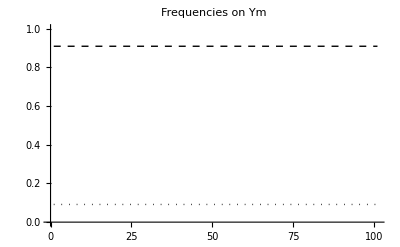

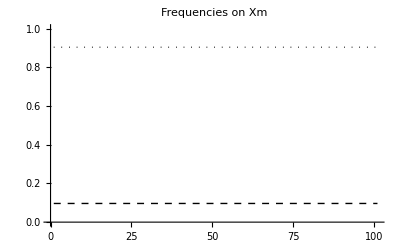

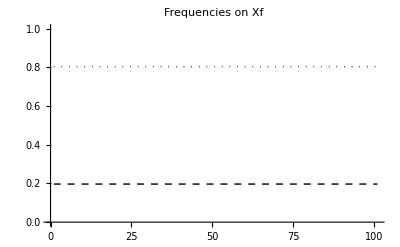

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryMdA)(initialpXm+devXm),(1-tryMdA)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryMdA*(initialpYm+devYm),tryMdA*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryMdA,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryMdA)(initialpXm+devXm),(1-tryMdA)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryMdA*(initialpYm+devYm),tryMdA*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryMdA,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryMdA)(initialpXm+devXm),(1-tryMdA)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryMdA*(initialpYm+devYm),tryMdA*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryMdA),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryMdA)(initialpXm+devXm),(1-tryMdA)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryMdA*(initialpYm+devYm),tryMdA*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryMdA),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryMdA)(initialpXm+devXm),(1-tryMdA)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryMdA*(initialpYm+devYm),tryMdA*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryMdA)(initialpXm+devXm),(1-tryMdA)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryMdA*(initialpYm+devYm),tryMdA*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=5000;
tinterval=100;
tplotinterval=1000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

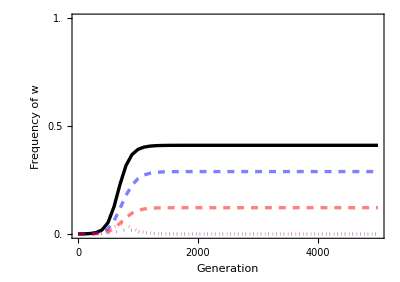

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

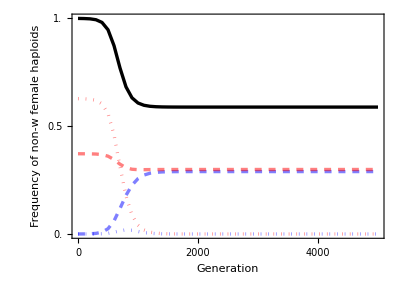

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

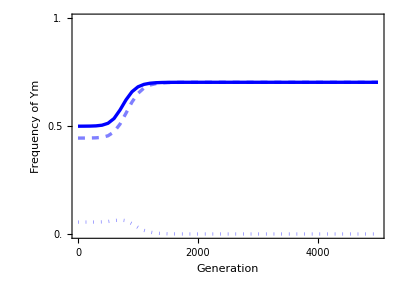

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

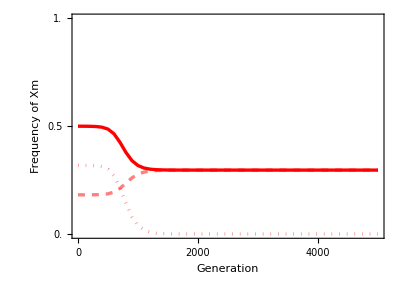

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio plot

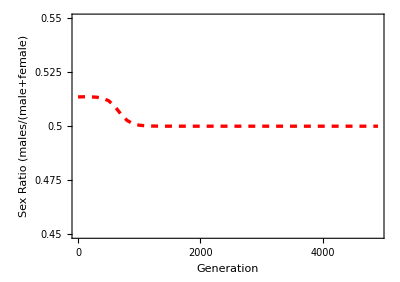

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

### Iterate Recursions (W appears to reach 50% after a long time, X not yet completely lost at the end of simulation though)

#### Parameters:

```mathematica
trysAf=0.07;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;

tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywA=1+tryt;
trywa=1;
tryr=0.01;
tryα=0.5;
```

Our invasion analysis indicates that invasion should occur when the following is positive (which assumes that hAm=hAf)

```mathematica
((-1+2 tryr) trysAf (trysAf-trysAm) tryt^2)/(2 tryr (trysAf+trysAm)^2)
```

0.0566942

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.770449

0.77974

0.147112

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

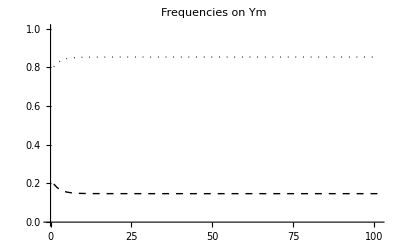

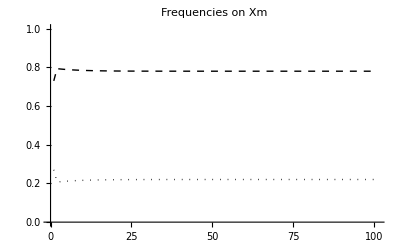

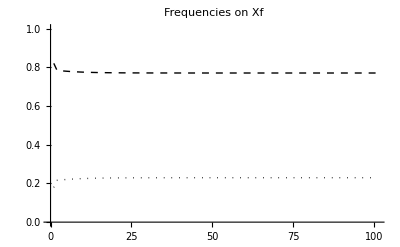

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=70000;
tinterval=100;
tplotinterval=10000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

$Aborted

Frequency of w at the end of the simulation:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.499104

which is increasing slightly.

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]-
Total[{nextYAwf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.0000192522

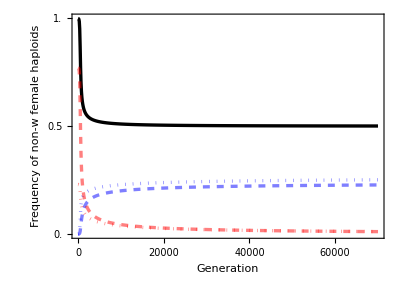

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

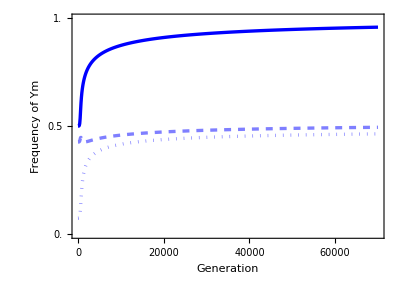

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

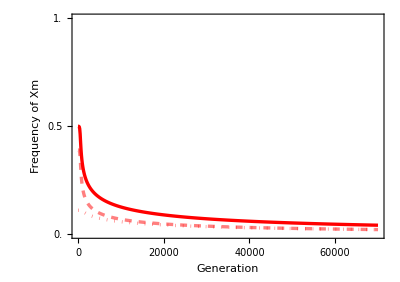

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio plot

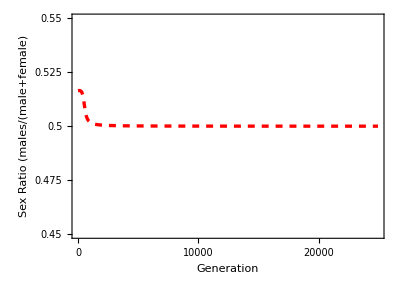

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

### Iterate Recursions (W invades but does not replace XY, polymorphic sex determination maintained without loss of variation)

#### Parameters:

```mathematica
trysAf=0.1;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;

tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywA=1+tryt;
trywa=1;
tryr=0.01;
tryα=0.5;
```

Our invasion analysis indicates that invasion should occur when the following is positive (which assumes that hAm=hAf)

```mathematica
((-1+2 tryr) trysAf (trysAf-trysAm) tryt^2)/(2 tryr (trysAf+trysAm)^2)
```

0.0392

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=1/2;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.834904

0.840045

0.15054

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

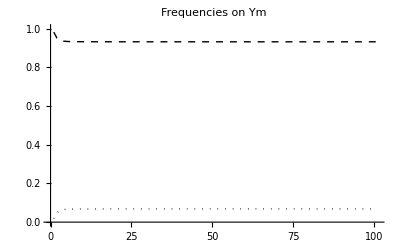

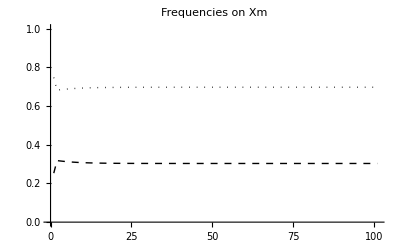

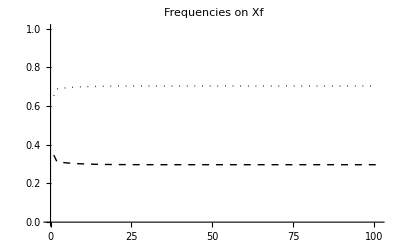

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=10000;
tinterval=100;
tplotinterval=2500;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

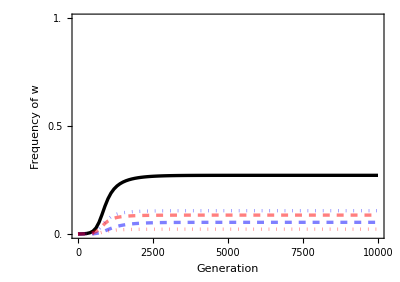

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

Frequency of w at the end of the simulation:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.272086

which is barely changing:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]-
Total[{nextYAwf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

3.70147×10^-8

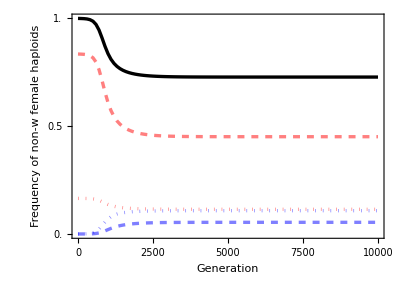

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

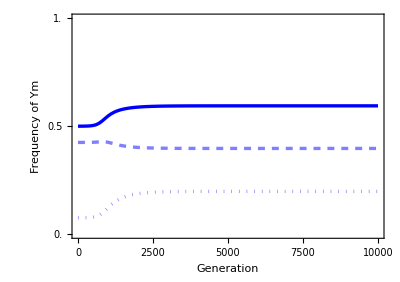

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

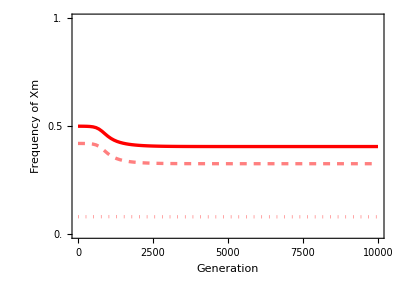

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio plot

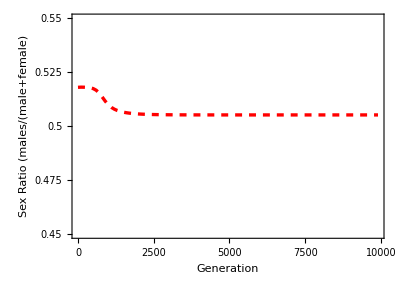

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

```mathematica
sexRatioAtBirth[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
```

0.505227